```mathematica
Vollständiges Modell
```

```mathematica
<<Statistics`ContinuousDistributions`
```

Get::noopen: Cannot open Statistics`ContinuousDistributions`.

$Failed

```mathematica
Clear["Global`*"];
ar=34; (* Number of reactions *)
am=24; (* Number of metabolites *)
$TextStyle=FontSize->14;  

(* List of parameters and rates *)

(*parameters*)
KPFvGLCtr=0.000213;
KadpPFvHK=0.000846735;
KadpPFvPFK=0.00074176;KadpPFvPGK=0.00015;KadpPFvPK=0.000317;KatpPFvHK=0.00069647;KatpPFvPFK=0.0007862;KatpPFvPGK=0.00077;Kb13pgPFvGAPDH=2.359*^-05;Kb13pgPFvPGK=1.34*^-05;KdPFvLACtr=(0.005*27*10^(-6))/43.52378275844468;KdPFvPYRtr=(0.0007*27*10^(-6))/43.52378275844468;KdhapPFvALD=0.00011;KdhapPFvG3PDH=0.00034;KdhapPFvTPI=0.001954;KeqPFvALD=9*^-05;KeqPFvENO=4.6;KeqPFvG3PDH=32600.0;KeqPFvHK=1310.0;KeqPFvPGI=0.33;KeqPFvPGK=3200.0;KeqPFvPGM=0.19;KeqPFvTPI=0.04545;Kf16bpPFvALD=6.84*^-05;Kf16bpPFvPFK=0.003626;Kf6pPFvPFK=0.00109454;Kf6pPFvPGI=9.6651*^-05;Kg3pPFvG3PDH=0.00398;Kg6pPFvHK=4.3*^-05;Kg6pPFvPGI=0.00100774;KgapPFvALD=4.6*^-05;KgapPFvGAPDH=0.000917;KgapPFvTPI=0.000337;KglcPFvHK=0.000168613;Ki1CytGlcTr=8.86746353676*^-08;Ki2CytGlcTr=2.07687280949*^-05;KiadpPFvPK=0.002;KiatpPFvHK=0.026;KiatpPFvPK=0.00182;KilacPFvPYRtr=0.000358;KipepPFvPK=0.00292;KipepPFvTPI=1.59*^-05;KipyrPFvLACtr=0.00163;KipyrPFvPK=0.105;KlacPFvLACtr=0.0038;KlacPFvLDH=0.003611;KmPFvATPASE=0.0045;KnadPFvG3PDH=0.00051;KnadPFvGAPDH=0.0005662;KnadPFvLDH=0.000234;KnadhPFvG3PDH=9*^-05;KnadhPFvGAPDH=2.87*^-05;KnadhPFvLDH=4.6*^-05;Kp2gPFvENO=0.000521;Kp2gPFvPGM=0.000318;Kp3gPFvPGK=0.000267;Kp3gPFvPGM=0.00173;KpepPFvENO=0.00129;KpepPFvPK=0.000406;KpyrPFvLDH=0.000133;KpyrPFvPYRtr=0.0157;LPFvPK=0.255;
VPFvALD=(0.0569593147718*27*10^(-6))/43.52378275844468;
VPFvATPASE=(0.135*27*10^(-6))/43.52378275844468;
VPFvENO=(0.286295503195*27*10^(-6))/43.52378275844468;VPFvGAPDH=(0.656263383259*27*10^(-6))/43.52378275844468;VPFvGLCtr=(0.0469*27*10^(-6))/43.52378275844468;VPFvHK=(0.083*27*10^(-6))/43.52378275844468;VPFvLACtr=(0.598*27*10^(-6))/43.52378275844468;VPFvPFK=0.41*27*10^(-6)/43.52378275844468;VPFvPGI=(0.800428265477*27*10^(-6))/43.52378275844468;VPFvPGM=(0.186937901488*27*10^(-6))/43.52378275844468;VPFvPK=(0.762*27*10^(-6))/43.52378275844468;VPFvPYRtr=(0.216*27*10^(-6))/43.52378275844468;VPFvTPI=(1.50599571726*27*10^(-6))/43.52378275844468;VfPFvG3PDH=(0.012*27*10^(-6))/43.52378275844468;VfPFvLDH=(0.542612419668*27*10^(-6))/43.52378275844468;VrPFvGAPDH=(0.243199143455*27*10^(-6))/43.52378275844468;VrPFvLDH=(0.290792291203*27*10^(-6))/43.52378275844468;VrPFvPGK=(0.353533190557*27*10^(-6))/43.52378275844468;
alphaPFvGLCtr=0.91;
cytb=0;
h=4.0;kPFvGLYtr=(2.0*27*10^(-6))/43.52378275844468;pHConversionFactor=1.0;phEX=7.1;(*phPF->7.2,*)
glcEX=1000*0.45/90;glyEX=1000*0.013499999999999998/90;lacEX=1000*0.18/90;pyrEX=1000*0.018000000000000002/90;Vex=1000;Vpf=1000; 

(*parameters IRIP*)
Nasal=125;
Ksal=5;
Clsal=130; 
pHsal=7.1; 
F=96485.33289;
Cm=0.01; 
zH=1; 
zNa=1;
zK= 1;
zCl= -1; 
phiKNaCl=0.92; 
Ysal= 70.8; 
R= 8.3144598; 
T= 310; 
Kcp= 1.5*10^(-12); 
zY= 0; 
bcp= 54.186505397223954; 
bcbp= 368.00427412088493; 
bcpkap= 7.172371123455439; 
KmNaHpumpHsal= 4.0976860324961274*10^(-06); 
KIPfATP4Hp= 7.104526671732046*10^(-06); 
KmNaHpumpNap= 0.6840120477024911; 
vmaxNaHpump= 7.703685608134962*10^(-08);
 sPfATP4H= 1; 
sPfATP4Na= 1; 
kVTypepumpEp0= -0.0999999978223507; 
vmaxVTypepump= (6.7024838393612216*10^(-06))/2; 
kexpVTypepump= 4.506272510067805; 
KmVTypepumpHp= 0.0022634396699840083;
sVtypeH= 4; 
sVtypeHexponent= 1; 
KIVTypeHsal= 0.0023696056686678623; 
kexpPfKchannel= 28.622973488515083; 
kPfKchannelEp0= -0.04375853867278892; 
keqPfKchannel= 0.9161672755776934;
kPfKchannel= 6.828228224275584*10^(-12);
kPfHClcot= 8.272568285457453*10^(-11);
hPfHClKIHp= 4.79709902173202; 
KmPfHClClrbc= 7.8; 
sPfHClCl= 1; 
sPfHClH= 1; 
KIPfHClHp= 2.928504560811203*10^(-05); 
PHp= 2.6440241005783135*10^(-05); 
PNap= 1.0346068948554299*10^(-10); 
PKp= 0;
PClp= 6.696605288022938*10^(-11); 
solidVp= 22.05;
cipargamin= 0;
concanamycin=0;
bafilomycin=0; 
KIcip= 0.5*10^(-6);
KIcona= 1.5*10^(-6);
KIbaf= 2*10^(-6);
caesium= 0; 
KIcs= 0.05; 
hclinhi= 0; 
KIhclinhi= 0.05; 
mercury= 0;
KImercury= 0.35; 
Atpss= 2.5;
KmAtpAtp4= 0.23; 
KmAtpVType= 0.2; 
sPfATP4ATP= 1.0;
 sVtypeATP= 1;

at=3.0;nt=3.0;

(*rates*)
v[1]=(1/60((VPFvALD*m[3]*(1-(m[2]*m[7])/(KeqPFvALD*Vpf*m[3])))/(Kf16bpPFvALD*(1+m[2]/(KdhapPFvALD*Vpf)+m[3]/(Kf16bpPFvALD*Vpf)+m[7]/(KgapPFvALD*Vpf)+(m[2]*m[7])/(KdhapPFvALD*KgapPFvALD*Vpf^2)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[2]=(1/60((VPFvATPASE*m[20]^5)/(KmPFvATPASE^5*Vpf^4*(1+m[20]^5/(KmPFvATPASE^5*Vpf^5)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[3]=(1/60((VPFvENO*m[10]*(1-m[12]/(KeqPFvENO*m[10])))/(Kp2gPFvENO*(1+m[10]/(Kp2gPFvENO*Vpf)+m[12]/(KpepPFvENO*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[4]=(1/60((VfPFvG3PDH*m[2]*m[21]*(1-(m[5]*m[22])/(KeqPFvG3PDH*m[2]*m[21])))/(KdhapPFvG3PDH*KnadhPFvG3PDH*Vpf*(1+m[2]/(KdhapPFvG3PDH*Vpf)+m[5]/(Kg3pPFvG3PDH*Vpf))*(1+m[21]/(KnadhPFvG3PDH*Vpf)+m[22]/(KnadPFvG3PDH*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[5]=(1/60((-((VrPFvGAPDH*m[1]*m[21])/(Kb13pgPFvGAPDH*KnadhPFvGAPDH*Vpf))+(VPFvGAPDH*m[7]*m[22])/(KgapPFvGAPDH*KnadPFvGAPDH*Vpf))/((1+m[1]/(Kb13pgPFvGAPDH*Vpf)+m[7]/(KgapPFvGAPDH*Vpf))*(1+m[21]/(KnadhPFvGAPDH*Vpf)+m[22]/(KnadPFvGAPDH*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[6]=(1/60(((glcEX*Vpf*VPFvGLCtr)/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vex)-(VPFvGLCtr*m[8])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr))/(1+(glcEX*(1+cytb/Ki2CytGlcTr))/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vex)+((1+cytb/Ki2CytGlcTr)*m[8])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vpf)+(alphaPFvGLCtr*glcEX*m[8])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr^2*Vex*Vpf))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));
v[7]=(1/60(kPFvGLYtr*Vpf*(-(glyEX/Vex)+m[5]/Vpf)))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[8]=(1/60((VPFvHK*m[20]*(1-(m[19]*m[6])/(KeqPFvHK*m[20]*m[8]))*m[8])/(KatpPFvHK*KglcPFvHK*Vpf*(1+m[19]/(KadpPFvHK*Vpf)+m[20]/(KatpPFvHK*Vpf))*(1+m[20]/(KiatpPFvHK*Vpf))*(1+m[6]/(Kg6pPFvHK*Vpf)+m[8]/(KglcPFvHK*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[9]=(1/60(KdPFvLACtr*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6))*(1-((pHConversionFactor/10^phEX)*lacEX*Vpf)/((pHConversionFactor/10^m[14])*Vex*m[9]))*m[9]+(VPFvLACtr*(1-((pHConversionFactor/10^phEX)*lacEX*Vpf)/((pHConversionFactor/10^m[14])*Vex*m[9]))*m[9])/(KlacPFvLACtr*(1+lacEX/(KlacPFvLACtr*Vex)+pyrEX/(KipyrPFvLACtr*Vex)+m[9]/(KlacPFvLACtr*Vpf)+m[13]/(KipyrPFvLACtr*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[10]=(1/60((-((VrPFvLDH*m[9]*m[22])/(KlacPFvLDH*KnadPFvLDH*Vpf))+(VfPFvLDH*m[21]*m[13])/(KnadhPFvLDH*KpyrPFvLDH*Vpf))/((1+m[21]/(KnadhPFvLDH*Vpf)+m[22]/(KnadPFvLDH*Vpf))*(1+m[9]/(KlacPFvLDH*Vpf)+m[13]/(KpyrPFvLDH*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[11]=(1/60((VPFvPFK*m[20]*m[4])/(KatpPFvPFK*Kf6pPFvPFK*Vpf*(1+m[20]/(KatpPFvPFK*Vpf))*(1+m[19]/(KadpPFvPFK*Vpf)+m[20]/(KatpPFvPFK*Vpf))*(1+m[3]/(Kf16bpPFvPFK*Vpf)+m[4]/(Kf6pPFvPFK*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[12]=(1/60((VPFvPGI*(1-m[4]/(KeqPFvPGI*m[6]))*m[6])/(Kg6pPFvPGI*(1+m[4]/(Kf6pPFvPGI*Vpf)+m[6]/(Kg6pPFvPGI*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[13]=(1/60((KadpPFvPGK*Kb13pgPFvPGK*KeqPFvPGK*VrPFvPGK*m[20]*(-1+(KeqPFvPGK*m[19]*m[1])/(m[20]*m[11]))*m[11])/(KatpPFvPGK^2*Kp3gPFvPGK^2*Vpf*(1+m[19]/(KadpPFvPGK*Vpf)+m[20]/(KatpPFvPGK*Vpf))*(1+m[1]/(Kb13pgPFvPGK*Vpf)+m[11]/(Kp3gPFvPGK*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[14]=(1/60((VPFvPGM*(1-m[10]/(KeqPFvPGM*m[11]))*m[11])/(Kp3gPFvPGM*(1+m[10]/(Kp2gPFvPGM*Vpf)+m[11]/(Kp3gPFvPGM*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[15]=(1/60((VPFvPK*m[19]*m[12])/(KadpPFvPK*KpepPFvPK*Vpf*(1+m[19]/(KadpPFvPK*Vpf))*(1+m[12]/(KpepPFvPK*Vpf))*(1+LPFvPK*(1+(m[19]/(KiadpPFvPK*Vpf)+m[20]/(KiatpPFvPK*Vpf))^h)*(1+(m[12]/(KipepPFvPK*Vpf)+m[13]/(KipyrPFvPK*Vpf))^h)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[16]=(1/60(KdPFvPYRtr*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6))*(1-((pHConversionFactor/10^phEX)*pyrEX*Vpf)/((pHConversionFactor/10^m[14])*Vex*m[13]))*m[13]+(VPFvPYRtr*(1-((pHConversionFactor/10^phEX)*pyrEX*Vpf)/((pHConversionFactor/10^m[14])*Vex*m[13]))*m[13])/(KpyrPFvPYRtr*(1+lacEX/(KilacPFvPYRtr*Vex)+pyrEX/(KpyrPFvPYRtr*Vex)+m[9]/(KilacPFvPYRtr*Vpf)+m[13]/(KpyrPFvPYRtr*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));v[17]=(1/60((VPFvTPI*m[2]*(1-m[7]/(KeqPFvTPI*m[2])))/(KdhapPFvTPI*(1+m[2]/(KdhapPFvTPI*Vpf)+m[7]/(KgapPFvTPI*Vpf)+m[12]/(KipepPFvTPI*Vpf)))))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));

v[18]= 
(vmaxNaHpump*((Atpss/(KmAtpAtp4+Atpss))^(-1))*((m[16]/(KmNaHpumpNap*(2^(1/sPfATP4Na)-1)*(1+(1*10^3*10^(-m[14]))/KIPfATP4Hp)+m[16]))^sPfATP4Na)*(((1*10^3*10^(-pHsal))/(KmNaHpumpHsal*(2^(1/sPfATP4H)-1)+(1*10^3*10^(-pHsal))))^sPfATP4H)*((m[20]/(KmAtpAtp4+m[20])))^1*(1/(1+cipargamin/KIcip)))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6));
v[19]=
(vmaxVTypepump*((Atpss/(KmAtpVType+Atpss))^(-1))*((m[20]/(KmAtpVType+m[20])))^1*(((1*10^3*10^(-m[14]))/((1*10^3*10^(-m[14]))+KmVTypepumpHp))^sVtypeHexponent)*(1/(1+Exp[-kexpVTypepump*(m[15]-kVTypepumpEp0)]))*(1/(1+(1*10^3*10^(-pHsal))/KIVTypeHsal))*(1/(1+concanamycin/KIcona))*(1/(1+bafilomycin/KIbaf))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6)));
v[20]=
(kPfHClcot*(R*T*
Log[m[18]^sPfHClCl*(1*10^3*10^(-m[14]))^sPfHClH/(Clsal^sPfHClCl*(1*10^3*10^(-pHsal))^sPfHClH)]+(sPfHClH-sPfHClCl)*F*m[15])*(1/(1+((1*10^3*10^(-m[14]))/KIPfHClHp)^hPfHClKIHp))*(1/(1+hclinhi/KIhclinhi))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6)));
v[21]=
(kPfKchannel*(1/(1+Exp[-kexpPfKchannel*(m[15]-kPfKchannelEp0)]))*((keqPfKchannel*m[15]-(R*T/(zK*F)*Log[(Ksal/m[17])]))*F)*(1/(1+caesium/KIcs))*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6)));
v[22]=
((PHp*zH*m[15]*F/(R*T))*((1*10^3*10^(-m[14]))-(1*10^3*10^(-pHsal))*Exp[-zH*m[15]*F/(R*T)])/(1-Exp[-zH*m[15]*F/(R*T)])*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6)));
v[23]=
((PNap*zNa*m[15]*F/(R*T))*(m[16]-Nasal*Exp[-zNa*m[15]*F/(R*T)])/(1-Exp[-zNa*m[15]*F/(R*T)])*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6)));
v[24]= 
((PKp*zK*m[15]*F/(R*T))*(m[17]-Ksal*Exp[-zK*m[15]*F/(R*T)])/(1-Exp[-zK*m[15]*F/(R*T)])*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6)));

v[25]=
 ((PClp*zCl*m[15]*F/(R*T))*(m[18]-Clsal*Exp[-zCl*m[15]*F/(R*T)])/(1-Exp[-zCl*m[15]*F/(R*T)])*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)/(m[23]*1*10^(-6)));
v[26]=1000000*(4*Pi(((3*m[23])/(4*Pi))^(1/3))^2)*Kcp*R*T*(((1*10^3*10^(-m[14]))+(m[16]+m[17]+m[18])*phiKNaCl+m[24])-((1*10^3*10^(-pHsal))+(Nasal+Ksal+Clsal)*phiKNaCl+Ysal));


v[27]=
vmaxVTypepump*((Atpss/(KmAtpVType+Atpss))^(-1))*((m[20]/(KmAtpVType+m[20])))^1*(((1*10^3*10^(-m[14]))/((1*10^3*10^(-m[14]))+KmVTypepumpHp))^sVtypeHexponent)*(1/(1+Exp[-kexpVTypepump*(m[15]-kVTypepumpEp0)]))*(1/(1+(1*10^3*10^(-pHsal))/KIVTypeHsal))*(1/(1+concanamycin/KIcona))*(1/(1+bafilomycin/KIbaf));
v[28]=
kPfKchannel*(1/(1+Exp[-kexpPfKchannel*(m[15]-kPfKchannelEp0)]))*((keqPfKchannel*m[15]-(R*T/(zK*F)*Log[(Ksal/m[17])]))*F);
v[29]= 
vmaxNaHpump*((Atpss/(KmAtpAtp4+Atpss))^(-1))*((m[16]/(KmNaHpumpNap*(2^(1/sPfATP4Na)-1)*(1+(1*10^3*10^(-m[14]))/KIPfATP4Hp)+m[16]))^sPfATP4Na)*(((1*10^3*10^(-pHsal))/(KmNaHpumpHsal*(2^(1/sPfATP4H)-1)+(1*10^3*10^(-pHsal))))^sPfATP4H)*((m[20]/(KmAtpAtp4+m[20])))^1*(1/(1+cipargamin/KIcip));
v[30]=
kPfHClcot*(R*T*
Log[m[18]^sPfHClCl*(1*10^3*10^(-m[14]))^sPfHClH/(Clsal^sPfHClCl*(1*10^3*10^(-pHsal))^sPfHClH)]+(sPfHClH-sPfHClCl)*F*m[15])*(1/(1+((1*10^3*10^(-m[14]))/KIPfHClHp)^hPfHClKIHp))*(1/(1+hclinhi/KIhclinhi));
v[31]=
(PHp*zH*m[15]*F/(R*T))*((1*10^3*10^(-m[14]))-(1*10^3*10^(-pHsal))*Exp[-zH*m[15]*F/(R*T)])/(1-Exp[-zH*m[15]*F/(R*T)]);
v[32]=
(PNap*zNa*m[15]*F/(R*T))*(m[16]-Nasal*Exp[-zNa*m[15]*F/(R*T)])/(1-Exp[-zNa*m[15]*F/(R*T)]);
v[33]= 
(PKp*zK*m[15]*F/(R*T))*(m[17]-Ksal*Exp[-zK*m[15]*F/(R*T)])/(1-Exp[-zK*m[15]*F/(R*T)]);
v[34]=
 (PClp*zCl*m[15]*F/(R*T))*(m[18]-Clsal*Exp[-zCl*m[15]*F/(R*T)])/(1-Exp[-zCl*m[15]*F/(R*T)]);



(* Calculation of elasticity coefficients *)
For[i=1,i≤ar,i++,
For[j=1,j≤am,j++,
drm[i,j]=D[v[i],m[j]]];
dvdsr[i]=Table[drm[i,j],{j,1,am}]];

dvds=Table[dvdsr[i],{i,1,ar}]; 

(* Reduced stoichiometric matrix, i.e. with conservation relations*)

(*v[1]=vPFvALD,v[2]=vPFvATPASE,v[3]=vPFvENO,v[4]=vPFvG3PDH,v[5]=vPFvGAPDH,v[6]=vPFvGLCtr,v[7]=vPFvGLYtr,v[8]=vPFvHK,v[9]=vPFvLACtr,v[10]=vPFvLDH,v[11]=vPFvPFK,v[12]=vPFvPGI,v[13]=vPFvPGK,v[14]=vPFvPGM,v[15]=vPFvPK,v[16]=vPFvPYRtr,v[17]=vPFvTPI, v[18]=JPfATP4salp,v[19]=JVtypesalp,v[20]=JPfHClsalp,v[21]=JPfKchannelsalp,v[22]=ghkfluxHsalp,v[23]=ghkfluxNasalp,v[24]=ghkfluxKsalp,v[25]=ghkfluxClsalp, v[26]=dVp, 
v[27]=JVtypesalp1, v[28]=JPfKchannelsalp1, v[29]=JPfATP4salp1, v[30]=JPfHClsalp1,v[31]=ghkfluxHsalp1,v[32]=ghkfluxNasalp1,v[33]=ghkfluxKsalp1,v[34]=ghkfluxClsalp1*)
nr= {
{0,0,0,0,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0} (*m[1]=b13pgPF'[t]*),
{1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0} (*m[2]=dhapPF'[t]*),
{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0} (*m[3]=f16bpPF'[t]*),
{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0} (*m[4]=f6pPF'[t]*),
{0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0} (*m[5]=g3pPF'[t]*),
{0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0} (*m[6]=g6pPF'[t]*),
{1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[7]=gapPF'[t]*),
{0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[8]=glcPF'[t]*),
{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[9]=lacPF'[t]*),
{0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[10]=p2gPF'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[11]=p3gPF'[t]*),
{0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[12]=pepPF'[t]*),
{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[13]=pyrPF'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-2,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0}(*m[14]=pHp'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,1,-1,-1,-1,-1}(*m[15]=Ep'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0}(*m[16]=Nap'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,-1,0,0,0,0,0,0,0,0}(*m[17]=Kp'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0}(*m[18]=Clp'[t]*),
{0,1,0,0,0,0,0,1,0,0,1,0,-1,0,-1,0,0,1,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0} (*m[19]=adpPF'[t]*),
{0,-1,0,0,0,0,0,-1,0,0,-1,0,1,0,1,0,0,-1,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0} (*m[20]=atpPF'[t]*),
{0,0,0,-1,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[21]=nadhPF'[t]*),
{0,0,0,1,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0}(*m[22]=nadPF'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0} (*m[23]=p'[t] and m[24]=Yp'*)
};


(* Link matrix; 
can be identity matrix if the system has no conservation relations. See Introduction to Computational Models of Biochemical Reaction Networks Chapter 7, p.131. 
24 rows and 22 columns. Columns and rows are both metabolites. First 22 rows make up identity matrix. The last 2 rows include the conservation relations that are missing from the reduces stoichiometric matrix nr. atpPF is -1 from adpPF (21 row) and nadPF is -1 from nadh (22nd row).  
Link matrix connects the reduced stoich. with the full matrix. *)
lr={
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}, 
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}
};

(*the calculations, first for the steady state *)
vv=Table[v[i],{i,1,ar}];
nv=nr.vv;
nvs=Table[nv[[i]]==0,{i,1,am-1}];

AppendTo[nvs,143.95504632741932==m[23]+m[24]]; (* conservation relations in this model *)


mlist=Table[{m[j],1},{j,1,am}];
Print["Concentrations"];
ss={m[1]->0.0006897975852698158,m[2]->1.4925889429857337,m[3]->1.7576642124146626,m[4]->0.2671492403896222,m[5]->1.0688745004213676,m[6]->0.8624960572141424,m[7]->0.06571901432602321,m[8]->0.746739940321222,m[9]->3.1706615402508476,m[10]->0.04371002804255525,m[11]->0.44098888166301553,m[12]->0.04748955119434503,m[13]->0.3185149094896996,m[14]->7.2998745746681815,m[15]->-0.09499272775144806, m[16]->10.018237278628614, m[17]->129.96758110167985, m[18]->69.94805814497622,m[19]->0.49855555609623214, m[20]->2.48142484088834, m[21]->0.14516924846889934, m[22]->2.8328911544652446, 
m[23]->27.022091456280386,m[24]->116.86086289636171}

Print["fluxes"];
fluss=Table[v[i]/.ss,{i,1,ar}]
```

Concentrations

{m[1]→0.000689798,m[2]→1.49259,m[3]→1.75766,m[4]→0.267149,m[5]→1.06887,m[6]→0.862496,m[7]→0.065719,m[8]→0.74674,m[9]→3.17066,m[10]→0.04371,m[11]→0.440989,m[12]→0.0474896,m[13]→0.318515,m[14]→7.29987,m[15]→-0.0949927,m[16]→10.0182,m[17]→129.968,m[18]→69.9481,m[19]→0.498556,m[20]→2.48142,m[21]→0.145169,m[22]→2.83289,m[23]→27.0221,m[24]→116.861}

fluxes

{0.151691,0.109122,0.27276,0.0306208,0.27276,0.151691,0.0306208,0.151691,0.242139,0.242139,0.151691,0.151691,0.27276,0.27276,0.27276,0.0306208,0.12107,0.0761153,0.0572235,-0.0261656,-2.7624×10^-18,-0.012166,-0.0761153,0.,0.0261656,0.,3.55083×10^-8,-1.71412×10^-24,4.72311×10^-8,-1.62363×10^-8,-7.54926×10^-9,-4.72311×10^-8,0.,1.62363×10^-8}

```mathematica
(* now calculating elasticities and control coefficients *)
dvdss=dvds/.ss;
(*Jakobi Matrix*)
Print["Jacobi-Matrix"];
mr=nr.dvdss.lr;

mra=Rationalize[mr,10^(-10)];
imra=Inverse[mra];
imr=N[imra]; 

MatrixForm[mra.imr] (*checks if product of matrix and its inverse is approximately identity matrix*)
```

Jacobi-Matrix

(1. | -9.83083×10^-13 | -1.17686×10^-12 | 4.14102×10^-13 | 2.74978×10^-14 | 1.45716×10^-12 | 5.05994×10^-13 | -1.17893×10^-13 | -2.00851×10^-17 | 7.48049×10^-13 | -2.45106×10^-14 | -1.59828×10^-14 | 2.75587×10^-16 | 1.27557×10^-11 | -0.00127255 | -5.0279×10^-11 | -5.23187×10^-11 | 1.64751×10^-12 | -0.0047525 | 0.00258244 | 9.46261×10^-6 | 0.0000206254 | 0.0020689
-6.938×10^-14 | 1. | -1.4365×10^-13 | -3.03016×10^-14 | 1.72917×10^-16 | 6.24816×10^-15 | -2.58746×10^-14 | -2.98327×10^-15 | -6.98407×10^-19 | 6.96343×10^-15 | -2.25356×10^-14 | 2.52594×10^-14 | -2.42831×10^-16 | 5.99798×10^-13 | 0.0000105104 | -1.3111×10^-12 | -1.991×10^-11 | -4.1809×10^-13 | 0.0000236358 | -0.0000656588 | -9.13404×10^-6 | -0.0000141837 | -0.000290968
8.36363×10^-16 | -2.52516×10^-15 | 1. | -1.77923×10^-15 | 4.43303×10^-17 | -4.58779×10^-15 | -1.97355×10^-15 | -4.1616×10^-17 | -3.75793×10^-19 | -8.12465×10^-16 | 2.20512×10^-16 | -1.21683×10^-15 | -6.36324×10^-17 | 6.27003×10^-14 | -2.99001×10^-6 | 6.93966×10^-13 | -1.25269×10^-12 | 4.54005×10^-14 | -4.10276×10^-6 | 0.000024441 | -1.02781×10^-6 | -3.4549×10^-6 | 0.0000208832
1.4279×10^-15 | -3.15126×10^-16 | 2.29969×10^-15 | 1. | 1.45378×10^-16 | 1.70145×10^-15 | 1.53615×10^-14 | 1.25785×10^-16 | -2.97654×10^-19 | 1.91279×10^-15 | 3.49914×10^-15 | 3.83642×10^-15 | 3.15605×10^-17 | -4.17439×10^-14 | -4.94672×10^-6 | 5.74062×10^-13 | 9.55765×10^-13 | -4.10303×10^-14 | -0.0000639011 | -4.2139×10^-6 | -7.89388×10^-7 | 4.88975×10^-6 | -0.0000105881
-2.0745×10^-15 | -1.97352×10^-15 | -2.77611×10^-15 | -2.46965×10^-15 | 1. | -2.47403×10^-15 | -2.92591×10^-15 | -2.63227×10^-16 | 1.3338×10^-19 | -3.11997×10^-16 | -1.68066×10^-16 | -1.54556×10^-15 | -8.7745×10^-19 | 4.64356×10^-14 | -8.03267×10^-7 | -8.3148×10^-13 | -9.64255×10^-13 | -1.60185×10^-13 | 0.000026616 | 0.0000362949 | -1.02781×10^-6 | -1.78597×10^-6 | 0.0000533081
4.31305×10^-16 | 7.96905×10^-15 | 7.25926×10^-15 | 8.21191×10^-15 | 9.13847×10^-17 | 1. | -8.17518×10^-15 | -7.80452×10^-17 | 1.83884×10^-19 | -1.24354×10^-15 | 2.52604×10^-16 | -2.38083×10^-15 | -3.54161×10^-17 | 4.82119×10^-14 | 4.21563×10^-6 | -7.95467×10^-12 | 9.11134×10^-13 | 4.41584×10^-13 | 0.0000672738 | -0.0000265656 | 1.83322×10^-6 | -5.93877×10^-7 | -0.0000740074
5.79166×10^-14 | -3.84981×10^-14 | 2.50176×10^-14 | -1.69945×10^-14 | -1.39831×10^-15 | 6.77552×10^-15 | 1. | -1.21413×10^-14 | 3.04019×10^-18 | -2.01971×10^-14 | 2.48996×10^-14 | -4.02394×10^-14 | 2.50922×10^-16 | 5.09773×10^-13 | -0.0000280957 | -2.09851×10^-11 | -1.31208×10^-11 | 9.57449×10^-13 | 0.000225114 | 0.000363659 | -2.45832×10^-6 | -5.12383×10^-6 | 0.000409505
-3.87485×10^-16 | 2.92894×10^-16 | -3.0044×10^-17 | 3.17182×10^-16 | -1.26987×10^-17 | -5.49355×10^-16 | 2.46898×10^-16 | 1. | -1.70744×10^-20 | -9.86259×10^-17 | 1.36378×10^-16 | -1.0661×10^-16 | -1.25284×10^-19 | -6.05022×10^-15 | 7.91498×10^-9 | -9.96214×10^-14 | 2.69869×10^-13 | -3.93095×10^-14 | 1.44071×10^-7 | -4.70564×10^-6 | 4.02705×10^-7 | -8.32296×10^-7 | -3.43553×10^-6
-5.43029×10^-15 | 3.26318×10^-15 | 5.79057×10^-14 | -4.10014×10^-14 | -9.52631×10^-16 | -2.98398×10^-14 | -2.689×10^-14 | -6.62192×10^-15 | 1. | 3.81302×10^-15 | -1.51517×10^-15 | -2.78265×10^-14 | 8.44123×10^-17 | -3.11492×10^-12 | 3.51928×10^-6 | -6.055×10^-11 | -5.33471×10^-11 | -3.2415×10^-13 | 0.000232929 | 0.000583906 | -2.6201×10^-6 | 6.2142×10^-6 | 0.000684476
7.74211×10^-17 | 2.74818×10^-17 | -6.1269×10^-17 | -1.15479×10^-17 | 9.08005×10^-19 | 4.21858×10^-17 | 2.3119×10^-17 | -7.78889×10^-18 | -4.58066×10^-21 | 1. | 4.53894×10^-18 | -3.8273×10^-18 | -2.066×10^-19 | 5.4961×10^-15 | 3.3992×10^-8 | 1.04346×10^-12 | -5.36819×10^-13 | -6.45969×10^-16 | -4.98193×10^-6 | -3.75196×10^-6 | 1.64287×10^-7 | -1.07071×10^-6 | -5.74507×10^-7
5.97875×10^-14 | -6.07538×10^-13 | -3.00653×10^-12 | -2.57045×10^-12 | -1.68773×10^-14 | -6.05682×10^-13 | -2.37047×10^-12 | 1.73558×10^-13 | 9.68283×10^-17 | -1.16197×10^-12 | 1. | -2.34915×10^-13 | 4.34186×10^-15 | -3.39645×10^-11 | 0.000817868 | -7.41666×10^-11 | -1.91595×10^-11 | -3.93609×10^-13 | -0.00567733 | -0.0084609 | -0.000109985 | -0.000123618 | -0.00791559
-1.61103×10^-16 | -9.13468×10^-17 | 8.9652×10^-17 | 7.25862×10^-17 | 9.90688×10^-18 | -1.49501×10^-16 | 7.77628×10^-17 | 1.8232×10^-17 | 9.92478×10^-21 | 1.3296×10^-16 | 3.5764×10^-17 | 1. | -7.10743×10^-20 | -4.5653×10^-15 | -4.30738×10^-7 | -3.96273×10^-13 | 2.76185×10^-14 | -4.19185×10^-14 | 2.48379×10^-7 | 3.02062×10^-6 | 6.41124×10^-7 | -3.55459×10^-7 | -2.95869×10^-6
-3.00471×10^-14 | -2.60033×10^-14 | 2.43215×10^-15 | -7.51761×10^-15 | 4.13744×10^-16 | 1.01894×10^-13 | 1.6555×10^-14 | 3.21186×10^-15 | -1.74707×10^-18 | 3.01112×10^-15 | -1.0682×10^-14 | 1.94463×10^-14 | 1. | 1.34116×10^-12 | -0.0000508283 | 1.05287×10^-10 | 8.62518×10^-12 | -3.26961×10^-13 | -0.000921304 | -0.00105642 | -0.0000165358 | 0.0000296382 | -0.000153027
-2.43241×10^-20 | -1.37048×10^-21 | -1.13877×10^-21 | 2.2432×10^-21 | 6.26662×10^-22 | -2.04325×10^-22 | -1.48998×10^-20 | 4.73054×10^-22 | -6.98715×10^-25 | 4.98775×10^-21 | -4.51582×10^-21 | 4.24219×10^-21 | -7.86733×10^-23 | 1. | 3.83191×10^-11 | -6.70583×10^-17 | 1.10363×10^-16 | -2.52834×10^-17 | -9.61903×10^-11 | 3.51113×10^-13 | -2.38655×10^-9 | -1.51441×10^-9 | 8.78022×10^-9
-3.7331×10^-27 | -2.75898×10^-27 | -1.06759×10^-27 | 1.43922×10^-27 | -2.55453×10^-30 | -1.36925×10^-27 | -1.59657×10^-27 | -5.29501×10^-28 | -5.60384×10^-32 | 8.17398×10^-28 | -1.41125×10^-27 | 3.65107×10^-28 | 1.23258×10^-29 | -1.69157×10^-23 | 1. | 1.09978×10^-24 | 2.46375×10^-22 | 8.99379×10^-25 | -2.65735×10^-17 | -1.67145×10^-17 | 6.08191×10^-17 | 2.60183×10^-16 | 1.16362×10^-15
2.2591×10^-19 | 5.93588×10^-19 | -2.28838×10^-18 | -1.13956×10^-18 | 1.49064×10^-19 | 4.02192×10^-18 | 1.43495×10^-18 | 1.3184×10^-18 | -2.7858×10^-23 | 1.12072×10^-18 | -6.65234×10^-19 | -3.57858×10^-19 | -1.68642×10^-20 | -5.96695×10^-15 | -2.32957×10^-9 | 1. | -4.13385×10^-15 | -4.41112×10^-14 | 9.96056×10^-9 | 1.80312×10^-8 | 4.02705×10^-7 | -8.32296×10^-7 | 3.79168×10^-7
-2.37618×10^-18 | 1.46095×10^-18 | 1.18106×10^-18 | -1.13956×10^-18 | 1.49064×10^-19 | 4.02192×10^-18 | 2.30231×10^-18 | 8.84723×10^-19 | -1.33737×10^-22 | 1.12072×10^-18 | 1.06949×10^-18 | -3.57858×10^-19 | -1.68642×10^-20 | 5.4961×10^-15 | 4.18969×10^-9 | 2.02826×10^-14 | 1. | -2.90677×10^-14 | 9.96056×10^-9 | 1.80312×10^-8 | 1.64287×10^-7 | -1.07071×10^-6 | 1.33284×10^-6
-2.37618×10^-18 | 1.46095×10^-18 | -2.28838×10^-18 | -2.72203×10^-19 | 4.06437×10^-20 | 1.41983×10^-18 | 1.43495×10^-18 | 1.3184×10^-18 | -1.33737×10^-22 | 1.12072×10^-18 | 2.02127×10^-19 | 5.09504×10^-19 | -1.68642×10^-20 | -5.54616×10^-16 | 9.77762×10^-9 | 6.51587×10^-15 | 7.19042×10^-15 | 1. | 9.96056×10^-9 | 2.54818×10^-8 | 4.02705×10^-7 | -1.07071×10^-6 | 1.80968×10^-6
-2.26327×10^-13 | -2.50243×10^-12 | -2.18473×10^-12 | 9.15147×10^-13 | 1.23887×10^-14 | 1.41777×10^-12 | 2.01479×10^-12 | 7.90011×10^-14 | -1.27425×10^-16 | 4.31051×10^-13 | -1.15348×10^-12 | -7.1023×10^-13 | 1.50902×10^-15 | 1.86178×10^-11 | -0.00207197 | 6.3729×10^-10 | -6.26807×10^-10 | -2.19717×10^-12 | 0.995326 | 0.00590774 | 0.0000226699 | 0.0000943988 | -0.00549662
-4.97839×10^-13 | 1.32574×10^-12 | 1.10144×10^-12 | -1.78251×10^-12 | -1.61884×10^-14 | -1.89385×10^-12 | -2.38282×10^-12 | 2.97857×10^-13 | 4.87758×10^-17 | -7.24667×10^-13 | 6.5091×10^-14 | -3.82588×10^-13 | -3.67505×10^-15 | -2.51197×10^-11 | 0.00152279 | -1.06316×10^-9 | 6.37422×10^-10 | 1.64611×10^-11 | 0.000362602 | 0.988099 | -0.000052074 | -0.0000619 | -0.00376591
3.24396×10^-14 | 8.79824×10^-15 | -1.20718×10^-13 | 6.85014×10^-14 | -9.39963×10^-16 | 8.33367×10^-14 | 1.03166×10^-13 | 6.51998×10^-15 | -3.69758×10^-19 | -7.70279×10^-15 | -5.78684×10^-15 | -3.11809×10^-15 | -2.46892×10^-17 | 2.88541×10^-12 | 0.0000360436 | 1.35017×10^-10 | 1.93291×10^-11 | 1.17308×10^-12 | -0.000458983 | -0.00150264 | 0.999956 | 0.0000296853 | -0.00143776
-3.10635×10^-14 | -7.19764×10^-15 | -6.47873×10^-14 | -2.66656×10^-14 | -1.38221×10^-15 | -1.5417×10^-13 | -1.07098×10^-13 | -3.32718×10^-15 | 5.0089×10^-18 | -3.18311×10^-14 | -4.48232×10^-15 | -2.46824×10^-14 | 1.07109×10^-16 | -1.44337×10^-12 | 0.0000671237 | -1.33521×10^-10 | -2.65609×10^-11 | 5.2238×10^-13 | 0.000936481 | 0.00127492 | -2.2199×10^-6 | 0.999986 | 0.000742338
3.04902×10^-19 | -1.05747×10^-19 | 2.2259×10^-18 | 2.4245×10^-18 | -1.40594×10^-19 | -1.78439×10^-18 | -2.11783×10^-18 | -1.06221×10^-18 | 6.25927×10^-23 | -1.35614×10^-18 | 8.26814×10^-19 | 2.13669×10^-19 | 1.90707×10^-20 | -1.45354×10^-15 | -8.57537×10^-9 | -1.67657×10^-14 | -1.91769×10^-14 | 3.95426×10^-14 | 4.96504×10^-9 | -1.80074×10^-8 | -8.57407×10^-8 | 1.95586×10^-7 | 0.999998)

```mathematica
ga=-lr.imr.nr;
MatrixForm[Simplify[ga]];
fi=IdentityMatrix[ar]+dvdss.ga;
Print["Matrix der unnormierten FlussKK"];
MatrixForm[Simplify[fi]]
```

Matrix der unnormierten FlussKK

(0.0121392 | -0.615124 | 0.32219 | -0.24653 | 0.0301873 | 0.0933195 | -0.0101495 | 0.105862 | 0.0000222851 | 0.0120786 | 0.0957022 | 0.00517596 | 0.0000725615 | 0.334385 | 0.25936 | -0.00170911 | 0.00147644 | 1460.93 | 126.389 | -17.2124 | -925.045 | 63.5019 | 1398.04 | -925.045 | -80.7143 | 0.244318 | -3.59082×10^9 | 0. | 0. | 1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9
0.0000632114 | 0.999401 | -0.000148907 | -0.00128374 | 0.000157148 | 0.000485936 | -0.0000528509 | 0.000551347 | 1.16043×10^-7 | 0.0000628985 | 0.000498561 | 0.0000269524 | 4.40343×10^-7 | -0.000154543 | -0.0001347 | -8.89971×10^-6 | 7.68815×10^-6 | 2.0414 | -30.5042 | 2.88758 | 199.589 | -15.2518 | 17.2938 | 199.589 | 18.1394 | -0.0527183 | -1.5173×10^8 | 0. | 0. | 7.58648×10^7 | -7.58648×10^7 | -7.58648×10^7 | -7.58648×10^7 | -7.58648×10^7
0.0121702 | -0.115391 | 0.322117 | -0.24716 | 0.030264 | 0.093558 | -0.0101755 | 0.106156 | 0.000022342 | 0.0121118 | 0.0959921 | 0.00518919 | 0.0000300128 | 0.334309 | 0.259265 | -0.00171348 | 0.00148021 | 1461.99 | 111.194 | -15.7961 | -823.611 | 55.6545 | 1406.45 | -823.611 | -71.4506 | 0.217553 | -3.66686×10^9 | 0. | 0. | 1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9
0.0121081 | -1.1148 | 0.322263 | -0.2459 | 0.0301096 | 0.0930811 | -0.0101236 | 0.10562 | 0.0000222281 | 0.0120513 | 0.0955103 | 0.00516273 | 0.0000224357 | 0.334461 | 0.259398 | -0.00170474 | 0.00147267 | 1459.88 | 141.584 | -18.6286 | -1026.48 | 71.3494 | 1389.64 | -1026.48 | -89.978 | 0.271151 | -3.51478×10^9 | 0. | 0. | 1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9
0.0121702 | -0.115447 | 0.322117 | -0.247162 | 0.0302656 | 0.093558 | -0.0101755 | 0.106068 | 0.000022342 | 0.0121025 | 0.0958984 | 0.00518919 | 0.000142591 | 0.334309 | 0.259253 | -0.00171348 | 0.00148021 | 1461.99 | 111.193 | -15.7961 | -823.611 | 55.6545 | 1406.45 | -823.611 | -71.4506 | 0.217325 | -3.66686×10^9 | 0. | 0. | 1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9
0.0121392 | -0.615101 | 0.32219 | -0.24653 | 0.0301868 | 0.0933195 | -0.0101495 | 0.10588 | 0.0000222851 | 0.012081 | 0.0957422 | 0.00517596 | 0.0000348538 | 0.334385 | 0.259331 | -0.00170911 | 0.00147644 | 1460.93 | 126.389 | -17.2124 | -925.045 | 63.5019 | 1398.04 | -925.045 | -80.7143 | 0.244338 | -3.59082×10^9 | 0. | 0. | 1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9
0.0121081 | -1.11481 | 0.322263 | -0.2459 | 0.0301097 | 0.0930811 | -0.0101236 | 0.105611 | 0.0000222281 | 0.0120501 | 0.0954989 | 0.00516273 | 0.0000345726 | 0.334461 | 0.259399 | -0.00170474 | 0.00147267 | 1459.88 | 141.584 | -18.6286 | -1026.48 | 71.3494 | 1389.64 | -1026.48 | -89.978 | 0.271131 | -3.51478×10^9 | 0. | 0. | 1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9
0.0121392 | -0.615098 | 0.32219 | -0.24653 | 0.0301866 | 0.0933195 | -0.0101495 | 0.105884 | 0.0000222851 | 0.012081 | 0.0957473 | 0.00517596 | 0.0000331335 | 0.334385 | 0.259333 | -0.00170911 | 0.00147644 | 1460.93 | 126.389 | -17.2124 | -925.045 | 63.5019 | 1398.04 | -925.045 | -80.7143 | 0.244342 | -3.59082×10^9 | 0. | 0. | 1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9
0.0000620488 | 0.999411 | -0.00014608 | -0.00125986 | 0.000155641 | 0.000477008 | -0.0000518901 | 0.000541219 | 1.13925×10^-7 | 0.0000630158 | 0.000489449 | 0.0000264572 | 4.89742×10^-7 | -0.000151609 | -0.00013217 | -8.73723×10^-6 | 7.54729×10^-6 | 2.11083 | -30.3903 | 2.83246 | 202.868 | -15.6949 | 16.8063 | 202.868 | 18.5273 | -0.0535715 | -1.52084×10^8 | 0. | 0. | 7.60421×10^7 | -7.60421×10^7 | -7.60421×10^7 | -7.60421×10^7 | -7.60421×10^7
0.000062047 | 0.999694 | -0.00014611 | -0.0012497 | 0.000145878 | 0.000476994 | -0.0000518847 | 0.000962858 | 1.13916×10^-7 | 0.000111332 | 0.000979795 | 0.0000264564 | -0.000542434 | -0.000151641 | -0.000134225 | -8.73656×10^-6 | 7.5469×10^-6 | 2.1108 | -30.3898 | 2.83246 | 202.868 | -15.6949 | 16.8062 | 202.868 | 18.5273 | -0.0525198 | -1.52084×10^8 | 0. | 0. | 7.60419×10^7 | -7.60419×10^7 | -7.60419×10^7 | -7.60419×10^7 | -7.60419×10^7
0.0121392 | -0.615104 | 0.32219 | -0.24653 | 0.030187 | 0.0933195 | -0.0101495 | 0.105879 | 0.0000222851 | 0.0120808 | 0.0957431 | 0.00517596 | 0.0000363073 | 0.334385 | 0.259337 | -0.00170911 | 0.00147644 | 1460.93 | 126.389 | -17.2124 | -925.045 | 63.5019 | 1398.04 | -925.045 | -80.7143 | 0.244338 | -3.59082×10^9 | 0. | 0. | 1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9
0.0121392 | -0.61506 | 0.32219 | -0.246534 | 0.0301921 | 0.0933195 | -0.0101495 | 0.10592 | 0.0000222851 | 0.0120787 | 0.095762 | 0.00517596 | -4.95972×10^-6 | 0.334385 | 0.259252 | -0.00170911 | 0.00147644 | 1460.93 | 126.389 | -17.2124 | -925.045 | 63.5019 | 1398.04 | -925.045 | -80.7143 | 0.244315 | -3.59082×10^9 | 0. | 0. | 1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9 | -1.79541×10^9
0.0121702 | -0.11875 | 0.322117 | -0.247135 | 0.030259 | 0.093558 | -0.0101755 | 0.100863 | 0.000022342 | 0.0121563 | 0.0905546 | 0.00518919 | 0.00443611 | 0.334309 | 0.263745 | -0.00171348 | 0.00148021 | 1461.98 | 111.19 | -15.7961 | -823.611 | 55.6545 | 1406.45 | -823.611 | -71.4506 | 0.208889 | -3.66686×10^9 | 0. | 0. | 1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9
0.0121702 | -0.115395 | 0.322117 | -0.24716 | 0.0302641 | 0.093558 | -0.0101755 | 0.106151 | 0.000022342 | 0.0121119 | 0.0959853 | 0.00518919 | 0.0000350037 | 0.334309 | 0.259264 | -0.00171348 | 0.00148021 | 1461.99 | 111.194 | -15.7961 | -823.611 | 55.6545 | 1406.45 | -823.611 | -71.4506 | 0.217539 | -3.66686×10^9 | 0. | 0. | 1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9
0.0121702 | -0.115394 | 0.322117 | -0.24716 | 0.0302641 | 0.093558 | -0.0101755 | 0.106152 | 0.000022342 | 0.0121118 | 0.0959891 | 0.00518919 | 0.0000367086 | 0.334309 | 0.259265 | -0.00171348 | 0.00148021 | 1461.99 | 111.194 | -15.7961 | -823.611 | 55.6545 | 1406.45 | -823.611 | -71.4506 | 0.217537 | -3.66686×10^9 | 0. | 0. | 1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9 | -1.83343×10^9
0.0121081 | -1.11481 | 0.322263 | -0.2459 | 0.0301099 | 0.093081 | -0.0101236 | 0.105609 | 0.0000222281 | 0.0120499 | 0.0954989 | 0.00516273 | 0.000036316 | 0.334461 | 0.2594 | -0.00170474 | 0.00147266 | 1459.88 | 141.584 | -18.6286 | -1026.48 | 71.3493 | 1389.64 | -1026.48 | -89.9779 | 0.271137 | -3.51478×10^9 | 0. | 0. | 1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9 | -1.75739×10^9
0.0000310218 | 0.499785 | -0.0000730825 | -0.000631075 | 0.0000873755 | 0.000238484 | -0.0000259373 | 0.000365143 | 5.695×10^-8 | 0.000032676 | 0.000290446 | 0.0000132275 | -0.0000967456 | -0.0000758487 | -0.000124042 | -4.36766×10^-6 | 3.77308×10^-6 | 1.05524 | -15.1952 | 1.41623 | 101.434 | -7.84745 | 8.40297 | 101.434 | 9.26368 | -0.0272611 | -7.60417×10^7 | 0. | 0. | 3.80208×10^7 | -3.80208×10^7 | -3.80208×10^7 | -3.80208×10^7 | -3.80208×10^7
-9.48014×10^-7 | 8.98876×10^-6 | 2.23324×10^-6 | 0.0000192532 | -2.3579×10^-6 | -7.28784×10^-6 | 7.92632×10^-7 | -8.26889×10^-6 | -1.74036×10^-9 | -9.43509×10^-7 | -7.4772×10^-6 | -4.04219×10^-7 | -6.56934×10^-9 | 2.31776×10^-6 | 2.02021×10^-6 | 1.33474×10^-7 | -1.15303×10^-7 | 0.0721544 | -0.254164 | 0.128111 | 3.54859 | -0.127087 | -0.800768 | 3.54859 | 0.255198 | -0.000937307 | 232150. | 0. | 0. | -116075. | 116075. | 116075. | 116075. | 116075.
-2.17428×10^-7 | 2.06157×10^-6 | 5.12194×10^-7 | 4.41676×10^-6 | -5.41736×10^-7 | -1.67147×10^-6 | 1.81791×10^-7 | -1.89649×10^-6 | -3.99154×10^-10 | -2.15459×10^-7 | -1.71491×10^-6 | -9.2708×10^-8 | -1.49282×10^-9 | 5.31581×10^-7 | 4.63346×10^-7 | 3.06123×10^-8 | -2.64449×10^-8 | -0.00309329 | 0.367969 | -0.183227 | -0.26901 | -0.316017 | 0.312921 | -0.26901 | 0.132789 | 0.0000710582 | -585815. | 0. | 0. | 292908. | -292908. | -292908. | -292908. | -292908.
1.23611×10^-6 | -0.0000117204 | -2.91191×10^-6 | -0.0000251025 | 3.07288×10^-6 | 9.50259×10^-6 | -1.03351×10^-6 | 0.0000107818 | 2.26926×10^-9 | 1.23138×10^-6 | 9.7495×10^-6 | 5.27061×10^-7 | 8.59888×10^-9 | -3.02213×10^-6 | -2.63412×10^-6 | -1.74036×10^-7 | 1.50344×10^-7 | -0.0549027 | -0.523336 | 0.260867 | -2.40177 | -0.261662 | 0.206771 | -2.40177 | -0.477471 | 0.000634396 | 979245. | 0. | 0. | -489622. | 489622. | 489622. | 489622. | 489622.
3.53968×10^-13 | -9.65937×10^-12 | -8.33843×10^-13 | -2.11961×10^-10 | 7.16724×10^-11 | 2.72112×10^-12 | -2.95952×10^-13 | -4.07798×10^-12 | 6.49815×10^-16 | -9.34353×10^-11 | -4.98691×10^-12 | 1.50927×10^-13 | 6.11726×10^-12 | -8.65404×10^-13 | 4.91482×10^-12 | -4.98362×10^-14 | 4.30518×10^-14 | 1.67496×10^-8 | -1.0462×10^-7 | 5.25259×10^-8 | -1.6747×10^-7 | -5.2305×10^-8 | 6.90666×10^-8 | -1. | 1.04831×10^-7 | -2.40612×10^-10 | 0.128313 | 0. | 0. | -0.0641567 | 0.0641567 | 0.0641567 | 0.0641567 | 0.0641567
1.46756×10^-7 | -1.3915×10^-6 | -3.45714×10^-7 | -2.98049×10^-6 | 3.64898×10^-7 | 1.12819×10^-6 | -1.22703×10^-7 | 1.28005×10^-6 | 2.69415×10^-10 | 1.46044×10^-7 | 1.1575×10^-6 | 6.25747×10^-8 | 1.01966×10^-9 | -3.58799×10^-7 | -3.12734×10^-7 | -2.06622×10^-8 | 1.78494×10^-8 | -0.0110651 | 0.0415619 | -0.0225235 | -0.608806 | 1.02078 | -0.0318454 | -0.608806 | -0.0433051 | 0.000160807 | -39764.4 | 0. | 0. | 19882.2 | -19882.2 | -19882.2 | -19882.2 | -19882.2
9.48014×10^-7 | -8.98878×10^-6 | -2.23324×10^-6 | -0.0000192533 | 2.35721×10^-6 | 7.28784×10^-6 | -7.92632×10^-7 | 8.26887×10^-6 | 1.74036×10^-9 | 9.43378×10^-7 | 7.4772×10^-6 | 4.04219×10^-7 | 6.58656×10^-9 | -2.31776×10^-6 | -2.02019×10^-6 | -1.33474×10^-7 | 1.15303×10^-7 | -0.0721545 | 0.254164 | -0.128111 | -3.54859 | 0.127087 | 0.800768 | -3.54859 | -0.255198 | 0.000937309 | -232150. | 0. | 0. | 116075. | -116075. | -116075. | -116075. | -116075.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.23611×10^-6 | 0.0000117205 | 2.91191×10^-6 | 0.0000251039 | -3.07368×10^-6 | -9.50259×10^-6 | 1.03351×10^-6 | -0.0000107817 | -2.26926×10^-9 | -1.23056×10^-6 | -9.74946×10^-6 | -5.27061×10^-7 | -8.59755×10^-9 | 3.02213×10^-6 | 2.63411×10^-6 | 1.74036×10^-7 | -1.50344×10^-7 | 0.0549027 | 0.523336 | -0.260867 | 2.40177 | 0.261662 | -0.206771 | 2.40177 | 0.477471 | -0.00063439 | -979245. | 0. | 0. | 489622. | -489622. | -489622. | -489622. | -489622.
-8.71439×10^-14 | -1.95758×10^-8 | 2.05291×10^-13 | -8.5404×10^-7 | 7.11929×10^-7 | -6.69942×10^-13 | 7.28637×10^-14 | -2.67998×10^-8 | -1.59985×10^-16 | -7.2486×10^-7 | -2.50754×10^-8 | -3.71609×10^-14 | 1.92872×10^-8 | 2.13064×10^-13 | 1.93003×10^-8 | 1.22697×10^-14 | -1.05982×10^-14 | -2.39546×10^-8 | -1.76073×10^-8 | 1.16974×10^-10 | 4.21513×10^-10 | 1.75811×10^-10 | 1.03008×10^-9 | 4.21513×10^-10 | -5.88366×10^-11 | 1.20554×10^-6 | -0.00365208 | 0. | 0. | 0.00182604 | -0.00182604 | -0.00182604 | -0.00182602 | -0.00182602
6.31706×10^-13 | -5.98965×10^-12 | -1.48811×10^-12 | -1.28287×10^-11 | 1.57034×10^-12 | 4.85623×10^-12 | -5.28168×10^-13 | 5.50992×10^-12 | 1.15969×10^-15 | 6.29068×10^-13 | 4.9824×10^-12 | 2.6935×10^-13 | 4.39966×10^-15 | -1.54444×10^-12 | -1.34614×10^-12 | -8.89398×10^-14 | 7.6832×10^-14 | -1.24099×10^-8 | -3.92705×10^-7 | -1.13609×10^-7 | -1.62885×10^-7 | -1.96349×10^-7 | 1.83945×10^-7 | -1.62885×10^-7 | 8.27403×10^-8 | 4.30253×10^-11 | 0.664148 | 0. | 0. | 0.167926 | -0.167926 | -0.167926 | -0.167926 | -0.167926
2.19644×10^-19 | -5.99383×10^-18 | -5.17416×10^-19 | -1.31526×10^-16 | 4.44742×10^-17 | 1.68851×10^-18 | -1.83644×10^-19 | -2.53046×10^-18 | 4.03223×10^-22 | -5.79784×10^-17 | -3.09448×10^-18 | 9.36531×10^-20 | 3.79588×10^-18 | -5.37×10^-19 | 3.04974×10^-18 | -3.09244×10^-20 | 2.67145×10^-20 | 1.03934×10^-14 | -6.4919×10^-14 | 3.25934×10^-14 | -6.2052×10^-7 | -3.24563×10^-14 | 4.28572×10^-14 | -6.2052×10^-7 | 6.50497×10^-14 | -1.49305×10^-16 | 7.96209×10^-8 | 1. | 0. | -3.98105×10^-8 | 3.98105×10^-8 | 3.98105×10^-8 | 3.98105×10^-8 | 3.98105×10^-8
4.31458×10^-13 | -4.09096×10^-12 | -1.01639×10^-12 | -8.76252×10^-12 | 1.07278×10^-12 | 3.31682×10^-12 | -3.60741×10^-13 | 3.76329×10^-12 | 7.9207×10^-16 | 4.29119×10^-13 | 3.40299×10^-12 | 1.83967×10^-13 | 3.00791×10^-15 | -1.05486×10^-12 | -9.19411×10^-13 | -6.07462×10^-14 | 5.24765×10^-14 | -5.897×10^-7 | -1.58401×10^-7 | 7.96116×10^-8 | 2.20735×10^-6 | -7.91987×10^-8 | -5.10497×10^-7 | 2.20735×10^-6 | 1.5881×10^-7 | -5.83038×10^-10 | 0.180843 | 0. | 1. | -0.0904215 | 0.0904215 | 0.0904215 | 0.0904215 | 0.0904215
4.16491×10^-13 | -3.94904×10^-12 | -9.81128×10^-13 | -8.45745×10^-12 | 1.03503×10^-12 | 3.20177×10^-12 | -3.48227×10^-13 | 3.63276×10^-12 | 7.64594×10^-16 | 4.1532×10^-13 | 3.28496×10^-12 | 1.77586×10^-13 | 2.90045×10^-15 | -1.01826×10^-12 | -8.87532×10^-13 | -5.8639×10^-14 | 5.06562×10^-14 | -2.92714×10^-8 | -3.24504×10^-7 | -4.58686×10^-7 | -1.49219×10^-6 | -1.6225×10^-7 | 1.32982×10^-7 | -1.49219×10^-6 | -2.96437×10^-7 | 3.94143×10^-10 | 0.594994 | 0. | 0. | 0.702503 | 0.297497 | 0.297497 | 0.297497 | 0.297497
-7.19236×10^-14 | 6.81957×10^-13 | 1.6943×10^-13 | 1.46069×10^-12 | -1.78905×10^-13 | -5.52911×10^-13 | 6.01351×10^-14 | -6.27339×10^-13 | -1.32037×10^-16 | -7.15449×10^-14 | -5.67276×10^-13 | -3.06672×10^-14 | -4.99617×10^-16 | 1.75843×10^-13 | 1.53267×10^-13 | 1.01263×10^-14 | -8.74779×10^-15 | -4.63581×10^-9 | 2.58999×10^-8 | -1.39948×10^-8 | -3.78635×10^-7 | 1.29496×10^-8 | -1.75861×10^-8 | -3.78635×10^-7 | -2.69444×10^-8 | 1.00011×10^-10 | -0.0305549 | 0. | 0. | 0.0152775 | 0.984723 | -0.0152775 | -0.0152775 | -0.0152775
-4.31458×10^-13 | 4.09095×10^-12 | 1.01639×10^-12 | 8.76245×10^-12 | -1.07321×10^-12 | -3.31682×10^-12 | 3.60741×10^-13 | -3.76331×10^-12 | -7.9207×10^-16 | -4.292×10^-13 | -3.403×10^-12 | -1.83967×10^-13 | -2.99722×10^-15 | 1.05486×10^-12 | 9.19423×10^-13 | 6.07462×10^-14 | -5.24765×10^-14 | -3.08195×10^-8 | 1.58401×10^-7 | -7.96116×10^-8 | -2.20735×10^-6 | 7.91987×10^-8 | -1.10022×10^-7 | -2.20735×10^-6 | -1.5881×10^-7 | 5.83039×10^-10 | -0.180843 | 0. | 0. | 0.0904214 | -0.0904214 | 0.909579 | -0.0904214 | -0.0904214
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
-4.16491×10^-13 | 3.94905×10^-12 | 9.81128×10^-13 | 8.45832×10^-12 | -1.03553×10^-12 | -3.20177×10^-12 | 3.48227×10^-13 | -3.63276×10^-12 | -7.64594×10^-16 | -4.14808×10^-13 | -3.28494×10^-12 | -1.77586×10^-13 | -2.89963×10^-15 | 1.01826×10^-12 | 8.87524×10^-13 | 5.8639×10^-14 | -5.06562×10^-14 | 2.92714×10^-8 | 3.24504×10^-7 | -1.61833×10^-7 | 1.49219×10^-6 | 1.6225×10^-7 | -1.32982×10^-7 | 1.49219×10^-6 | -3.24083×10^-7 | -3.9414×10^-10 | -0.594994 | 0. | 0. | 0.297497 | -0.297497 | -0.297497 | -0.297497 | 0.702503)

```mathematica
dgj=DiagonalMatrix[fluss];
invdgj=Table[If[And[i==j,fluss[[i]]≠0],1/fluss[[i]],0],{i,1,ar},{j,1,ar}];
cj=invdgj.fi.dgj;

mss=Table[m[i]/.ss,{i,1,am}];
invdgs=Table[If[And[i==j,mss[[i]]≠0],1/mss[[i]],0],{i,1,am},{j,1,am}];
cs=invdgs.ga.dgj;
MatrixForm[Simplify[cj]]
```

(0.0121392 | -0.442502 | 0.579341 | -0.0497655 | 0.0542808 | 0.0933195 | -0.00204882 | 0.105862 | 0.000035573 | 0.0192808 | 0.0957022 | 0.00517596 | 0.000130475 | 0.60127 | 0.466365 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.0000878705 | 0.999401 | -0.000372208 | -0.000360232 | 0.000392806 | 0.000675502 | -0.0000148306 | 0.000766431 | 2.57499×10^-7 | 0.000139571 | 0.000693052 | 0.0000374667 | 1.10068×10^-6 | -0.000386296 | -0.000336696 | -2.49736×10^-6 | 8.52996×10^-6 | 1.42394 | -15.9964 | -0.692395 | -5.05257×10^-15 | 1.70043 | -12.0629 | 0. | 4.34953 | 0. | -49.373 | 0. | 0. | -11.288 | 5.24849 | 32.8366 | 0. | -11.288
0.00676822 | -0.0461639 | 0.322117 | -0.0277468 | 0.030264 | 0.0520306 | -0.00114232 | 0.0590366 | 0.0000198338 | 0.0107521 | 0.0533842 | 0.00288587 | 0.0000300128 | 0.334309 | 0.259265 | -0.000192359 | 0.00065702 | 407.976 | 23.3277 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.0599818 | -3.97275 | 2.87062 | -0.2459 | 0.268207 | 0.461109 | -0.0101236 | 0.523225 | 0.000175773 | 0.0952975 | 0.473143 | 0.0255754 | 0.00019985 | 2.97927 | 2.31064 | -0.00170474 | 0.00582268 | 3628.87 | 264.589 | 15.9182 | 9.2602×10^-14 | -28.348 | -3454.29 | 0. | -76.8865 | 0. | -4075.78 | 0. | 0. | -931.832 | 433.267 | 2710.68 | 0. | -931.832
0.00676822 | -0.0461861 | 0.322117 | -0.0277471 | 0.0302656 | 0.0520306 | -0.00114233 | 0.0589879 | 0.0000198338 | 0.0107439 | 0.0533321 | 0.00288587 | 0.000142591 | 0.334309 | 0.259253 | -0.000192359 | 0.00065702 | 407.976 | 23.3277 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.0121392 | -0.442485 | 0.579341 | -0.0497654 | 0.05428 | 0.0933195 | -0.00204882 | 0.10588 | 0.000035573 | 0.0192846 | 0.0957422 | 0.00517596 | 0.0000626718 | 0.60127 | 0.466313 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.0599818 | -3.97277 | 2.87062 | -0.2459 | 0.268208 | 0.461109 | -0.0101236 | 0.523181 | 0.000175773 | 0.0952885 | 0.473086 | 0.0255754 | 0.000307961 | 2.97927 | 2.31065 | -0.00170474 | 0.00582268 | 3628.87 | 264.589 | 15.9182 | 9.2602×10^-14 | -28.348 | -3454.29 | 0. | -76.8865 | 0. | -4075.78 | 0. | 0. | -931.832 | 433.267 | 2710.68 | 0. | -931.832
0.0121392 | -0.442483 | 0.579341 | -0.0497654 | 0.0542797 | 0.0933195 | -0.00204882 | 0.105884 | 0.000035573 | 0.0192846 | 0.0957473 | 0.00517596 | 0.0000595786 | 0.60127 | 0.466316 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.000038871 | 0.450391 | -0.000164553 | -0.000159321 | 0.000175324 | 0.000298826 | -6.56199×10^-6 | 0.000339052 | 1.13925×10^-7 | 0.0000630158 | 0.00030662 | 0.0000165743 | 5.51674×10^-7 | -0.000170782 | -0.000148884 | -1.1049×10^-6 | 3.77364×10^-6 | 0.663529 | -7.18198 | -0.306075 | -2.31438×10^-15 | 0.788572 | -5.28298 | 0. | 2.00206 | 0. | -22.3022 | 0. | 0. | -5.09888 | 2.37079 | 14.8326 | 0. | -5.09888
0.0000388699 | 0.450518 | -0.000164587 | -0.000158036 | 0.000164325 | 0.000298817 | -6.5613×10^-6 | 0.000603192 | 1.13916×10^-7 | 0.000111332 | 0.000613802 | 0.0000165739 | -0.000611029 | -0.000170817 | -0.000151199 | -1.10482×10^-6 | 3.77345×10^-6 | 0.663519 | -7.18185 | -0.306076 | -2.31438×10^-15 | 0.788573 | -5.28294 | 0. | 2.00207 | 0. | -22.3022 | 0. | 0. | -5.09887 | 2.37079 | 14.8325 | 0. | -5.09887
0.0121392 | -0.442487 | 0.579341 | -0.0497654 | 0.0542803 | 0.0933195 | -0.00204882 | 0.105879 | 0.000035573 | 0.0192843 | 0.0957431 | 0.00517596 | 0.0000652855 | 0.60127 | 0.466324 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.0121392 | -0.442456 | 0.579341 | -0.0497663 | 0.0542895 | 0.0933195 | -0.00204882 | 0.10592 | 0.000035573 | 0.0192809 | 0.095762 | 0.00517596 | -8.91825×10^-6 | 0.60127 | 0.46617 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.00676822 | -0.0475075 | 0.322117 | -0.0277441 | 0.030259 | 0.0520306 | -0.00114232 | 0.0560929 | 0.0000198338 | 0.0107916 | 0.0503602 | 0.00288587 | 0.00443611 | 0.334309 | 0.263745 | -0.000192359 | 0.00065702 | 407.975 | 23.3269 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.00676822 | -0.0461652 | 0.322117 | -0.0277468 | 0.0302641 | 0.0520306 | -0.00114232 | 0.0590341 | 0.0000198338 | 0.0107522 | 0.0533804 | 0.00288587 | 0.0000350037 | 0.334309 | 0.259264 | -0.000192359 | 0.00065702 | 407.976 | 23.3277 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.00676822 | -0.0461651 | 0.322117 | -0.0277468 | 0.0302641 | 0.0520306 | -0.00114232 | 0.0590345 | 0.0000198338 | 0.0107521 | 0.0533825 | 0.00288587 | 0.0000367086 | 0.334309 | 0.259265 | -0.000192359 | 0.00065702 | 407.976 | 23.3277 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.0599818 | -3.97277 | 2.87061 | -0.2459 | 0.268209 | 0.461108 | -0.0101236 | 0.523169 | 0.000175773 | 0.0952864 | 0.473086 | 0.0255753 | 0.000323491 | 2.97927 | 2.31065 | -0.00170474 | 0.00582268 | 3628.87 | 264.589 | 15.9182 | 9.2602×10^-14 | -28.348 | -3454.29 | 0. | -76.8865 | 0. | -4075.78 | 0. | 0. | -931.831 | 433.267 | 2710.68 | 0. | -931.831
0.0000388678 | 0.450462 | -0.000164649 | -0.000159611 | 0.00019685 | 0.000298801 | -6.56004×10^-6 | 0.000457495 | 1.139×10^-7 | 0.000065352 | 0.000363905 | 0.000016573 | -0.00021796 | -0.000170881 | -0.000279455 | -1.10466×10^-6 | 3.77308×10^-6 | 0.663419 | -7.18199 | -0.306076 | -2.31438×10^-15 | 0.788573 | -5.28286 | 0. | 2.00207 | 0. | -22.3021 | 0. | 0. | -5.09885 | 2.37078 | 14.8325 | 0. | -5.09885
-1.8893×10^-6 | 0.0000128866 | 8.00283×10^-6 | 7.74548×10^-6 | -8.44957×10^-6 | -0.000014524 | 3.18872×10^-7 | -0.0000164791 | -5.53647×10^-9 | -3.00151×10^-6 | -0.0000149013 | -8.0557×10^-7 | -2.35413×10^-8 | 8.30574×10^-6 | 7.23945×10^-6 | 5.36958×10^-8 | -1.83402×10^-7 | 0.0721544 | -0.191081 | -0.0440398 | -1.28787×10^-16 | 0.0203131 | 0.800768 | 0. | 0.0877275 | 0. | 0.108299 | 0. | 0. | 0.0247601 | -0.0115125 | -0.0720268 | 0. | 0.0247601
-5.76367×10^-7 | 3.93128×10^-6 | 2.44142×10^-6 | 2.36345×10^-6 | -2.58223×10^-6 | -4.43081×10^-6 | 9.72779×10^-8 | -5.0273×10^-6 | -1.68901×10^-9 | -9.11709×10^-7 | -4.54596×10^-6 | -2.45754×10^-7 | -7.11565×10^-9 | 2.53382×10^-6 | 2.20857×10^-6 | 1.63809×10^-8 | -5.59504×10^-8 | -0.00411451 | 0.367969 | 0.0837813 | 1.29862×10^-17 | 0.0671869 | -0.416229 | 0. | 0.0607182 | 0. | -0.36351 | 0. | 0. | -0.083108 | 0.0386421 | 0.24176 | 0. | -0.083108
-7.16615×10^-6 | 0.0000488792 | 0.0000303549 | 0.0000293767 | -0.0000320328 | -0.0000550896 | 1.20949×10^-6 | -0.0000625053 | -2.09999×10^-8 | -0.0000113953 | -0.000056521 | -3.05554×10^-6 | -8.9638×10^-8 | 0.0000315038 | 0.0000274591 | 2.03669×10^-7 | -6.95648×10^-7 | 0.159711 | 1.14452 | 0.260867 | -2.53563×10^-16 | -0.121663 | 0.601494 | 0. | 0.477471 | 0. | -1.32889 | 0. | 0. | -0.30382 | 0.141265 | 0.883809 | 0. | -0.30382
-19437.3 | 381569. | 82333.9 | 2.34956×10^6 | -7.07696×10^6 | -149424. | 3280.58 | 223932. | -56.9598 | 8.19011×10^6 | 273844. | -8287.79 | -604020. | 85450.2 | -485291. | 552.427 | -1886.86 | -4.61518×10^8 | 2.16723×10^9 | 4.97528×10^8 | -1.6747×10^-7 | -2.30359×10^8 | 1.90306×10^9 | 0. | -9.92964×10^8 | 0. | -1.64936×10^9 | 0. | 0. | -3.77087×10^8 | 1.75331×10^8 | 1.09694×10^9 | 0. | -3.77087×10^8
-1.82981×10^-6 | 0.0000124808 | 7.75084×10^-6 | 7.50162×10^-6 | -8.18094×10^-6 | -0.0000140666 | 3.08831×10^-7 | -0.0000159602 | -5.36214×10^-9 | -2.9067×10^-6 | -0.0000144321 | -7.80204×10^-7 | -2.28605×10^-8 | 8.0442×10^-6 | 7.01143×10^-6 | 5.2005×10^-8 | -1.77627×10^-7 | 0.0692277 | -0.195488 | -0.0484415 | -1.38235×10^-16 | 1.02078 | -0.199237 | 0. | 0.0931367 | 0. | 0.116058 | 0. | 0. | 0.026534 | -0.0123373 | -0.0771869 | 0. | 0.026534
-1.8893×10^-6 | 0.0000128866 | 8.00283×10^-6 | 7.74552×10^-6 | -8.4471×10^-6 | -0.000014524 | 3.18872×10^-7 | -0.0000164791 | -5.53648×10^-9 | -3.00109×10^-6 | -0.0000149013 | -8.0557×10^-7 | -2.3603×10^-8 | 8.30574×10^-6 | 7.23938×10^-6 | 5.36958×10^-8 | -1.83402×10^-7 | 0.0721545 | -0.191081 | -0.0440398 | -1.28787×10^-16 | 0.0203131 | 0.800768 | 0. | 0.0877275 | 0. | 0.108299 | 0. | 0. | 0.0247601 | -0.0115125 | -0.0720267 | 0. | 0.0247601
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-7.16615×10^-6 | 0.0000488792 | 0.0000303549 | 0.0000293784 | -0.0000320412 | -0.0000550896 | 1.20949×10^-6 | -0.0000625053 | -2.09999×10^-8 | -0.0000113877 | -0.0000565208 | -3.05554×10^-6 | -8.96241×10^-8 | 0.0000315038 | 0.000027459 | 2.03669×10^-7 | -6.95648×10^-7 | 0.159711 | 1.14452 | 0.260867 | -2.53563×10^-16 | -0.121663 | 0.601494 | 0. | 0.477471 | 0. | -1.32889 | 0. | 0. | -0.30382 | 0.141265 | 0.883809 | 0. | -0.30382
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2.69863×10^-6 | -0.000018407 | -0.0000114311 | -0.0000110629 | 0.0000120627 | 0.0000207457 | -4.55469×10^-7 | 0.0000235383 | 7.90817×10^-9 | 4.28976×10^-6 | 0.0000212847 | 1.15066×10^-6 | 3.37964×10^-8 | -0.0000118637 | -0.0000103405 | -7.66978×10^-8 | 2.61968×10^-7 | -0.0266018 | -0.632864 | 0.083717 | 1.26718×10^-17 | 0.0672742 | -0.394304 | 0. | 0.0609703 | 0. | 0.664148 | 0. | 0. | -0.0767845 | 0.035702 | 0.223365 | 0. | -0.0767845
-19437.3 | 381569. | 82333.9 | 2.34956×10^6 | -7.07696×10^6 | -149424. | 3280.58 | 223932. | -56.9598 | 8.19011×10^6 | 273844. | -8287.79 | -604020. | 85450.2 | -485291. | 552.427 | -1886.86 | -4.61518×10^8 | 2.16723×10^9 | 4.97528×10^8 | -1. | -2.30359×10^8 | 1.90306×10^9 | 0. | -9.92964×10^8 | 0. | -1.64936×10^9 | 1. | 0. | -3.77087×10^8 | 1.75331×10^8 | 1.09694×10^9 | 0. | -3.77087×10^8
1.3857×10^-6 | -9.45167×10^-6 | -5.86964×10^-6 | -5.68091×10^-6 | 6.19534×10^-6 | 0.0000106525 | -2.33875×10^-7 | 0.0000120864 | 4.06071×10^-9 | 2.19996×10^-6 | 0.0000109293 | 5.90842×10^-7 | 1.73707×10^-8 | -6.09181×10^-6 | -5.30962×10^-6 | -3.93829×10^-8 | 1.34516×10^-7 | -0.950333 | -0.191914 | -0.0441041 | -1.29101×10^-16 | 0.0204004 | 0.822693 | 0. | 0.0879795 | 0. | 0.135958 | 0. | 1. | 0.0310835 | -0.0144527 | -0.0904215 | 0. | 0.0310835
-3.89115×10^-6 | 0.0000265409 | 0.0000164824 | 0.0000159503 | -0.0000173879 | -0.0000299131 | 6.56739×10^-7 | -0.0000339398 | -1.14028×10^-8 | -6.19387×10^-6 | -0.0000306904 | -1.65913×10^-6 | -4.8726×10^-8 | 0.0000171063 | 0.00001491 | 1.1059×10^-7 | -3.7773×10^-7 | 0.137224 | 1.14369 | -0.739197 | -2.53878×10^-16 | -0.121576 | 0.623419 | 0. | 0.477723 | 0. | -1.30124 | 0. | 0. | 0.702503 | 0.138325 | 0.865414 | 0. | -0.297497
1.44519×10^-6 | -9.85742×10^-6 | -6.12164×10^-6 | -5.92477×10^-6 | 6.46397×10^-6 | 0.0000111099 | -2.43916×10^-7 | 0.0000126054 | 4.23504×10^-9 | 2.29477×10^-6 | 0.0000113985 | 6.16208×10^-7 | 1.80515×10^-8 | -6.35334×10^-6 | -5.53764×10^-6 | -4.10737×10^-8 | 1.40291×10^-7 | 0.0467404 | -0.196321 | -0.0485057 | -1.38549×10^-16 | 0.0208689 | -0.177311 | 0. | 0.0933888 | 0. | 0.143716 | 0. | 0. | 0.0328574 | 0.984723 | -0.0955816 | 0. | 0.0328574
1.3857×10^-6 | -9.45164×10^-6 | -5.86964×10^-6 | -5.68087×10^-6 | 6.1978×10^-6 | 0.0000106525 | -2.33875×10^-7 | 0.0000120865 | 4.06071×10^-9 | 2.20038×10^-6 | 0.0000109293 | 5.90842×10^-7 | 1.7309×10^-8 | -6.09181×10^-6 | -5.30968×10^-6 | -3.93829×10^-8 | 1.34516×10^-7 | 0.0496672 | -0.191914 | -0.0441041 | -1.29101×10^-16 | 0.0204004 | -0.177307 | 0. | 0.0879795 | 0. | 0.135958 | 0. | 0. | 0.0310835 | -0.0144527 | 0.909579 | 0. | 0.0310835
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-3.89115×10^-6 | 0.000026541 | 0.0000164824 | 0.000015952 | -0.0000173963 | -0.0000299131 | 6.56739×10^-7 | -0.0000339397 | -1.14028×10^-8 | -6.18623×10^-6 | -0.0000306902 | -1.65913×10^-6 | -4.87121×10^-8 | 0.0000171063 | 0.0000149099 | 1.1059×10^-7 | -3.7773×10^-7 | 0.137224 | 1.14369 | 0.260803 | -2.53878×10^-16 | -0.121576 | 0.623419 | 0. | -0.522277 | 0. | -1.30124 | 0. | 0. | -0.297497 | 0.138325 | 0.865414 | 0. | 0.702503)

Normierte Flusskontrollkoeffizienten

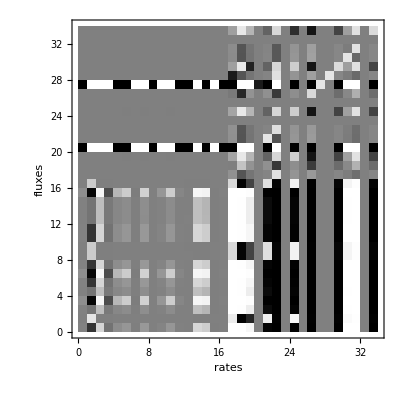

```mathematica
faktor=3;
cjp=ArcTan[cj*faktor]/Pi+0.5;
Print["Normierte Flusskontrollkoeffizienten"];
Show[Graphics[Raster[cjp]],AspectRatio->1,ImagePadding->1,Frame->True,FrameLabel->{"rates","fluxes"}, LabelStyle->Directive[Bold, Medium]]
```

Normierte Konzentrationskontrollkoeffizienten

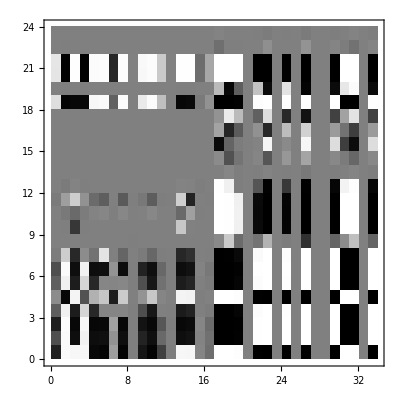

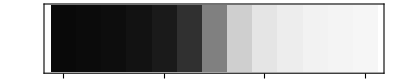

```mathematica
cjs=ArcTan[cs*faktor]/Pi+0.5;
Print["Normierte Konzentrationskontrollkoeffizienten"];
Show[Graphics[Raster[cjs]],AspectRatio->1,ImagePadding->1,Frame->True, LabelStyle->Directive[Black,Bold, Medium]]

massstab=ArcTan[Table[x/2,{y,1,1},{x,-6,6}]*faktor]/Pi+0.5;
Show[Graphics[Raster[massstab]],AspectRatio->0.2,Frame->True,FrameTicks->{{{0.5,-3},{2.5,-2},{4.5,-1},{6.5,0},{8.5,1},{10.5,2},{12.5,3}},None,None,None}, ColorFunction->"SunsetColors"]
```

```mathematica
cjw=MatrixForm[cj]
csw=MatrixForm[cs]
dvdsw=MatrixForm[dvds/.ss]
```

(0.0121392 | -0.442502 | 0.579341 | -0.0497655 | 0.0542808 | 0.0933195 | -0.00204882 | 0.105862 | 0.000035573 | 0.0192808 | 0.0957022 | 0.00517596 | 0.000130475 | 0.60127 | 0.466365 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.0000878705 | 0.999401 | -0.000372208 | -0.000360232 | 0.000392806 | 0.000675502 | -0.0000148306 | 0.000766431 | 2.57499×10^-7 | 0.000139571 | 0.000693052 | 0.0000374667 | 1.10068×10^-6 | -0.000386296 | -0.000336696 | -2.49736×10^-6 | 8.52996×10^-6 | 1.42394 | -15.9964 | -0.692395 | -5.05257×10^-15 | 1.70043 | -12.0629 | 0. | 4.34953 | 0. | -49.373 | 0. | 0. | -11.288 | 5.24849 | 32.8366 | 0. | -11.288
0.00676822 | -0.0461639 | 0.322117 | -0.0277468 | 0.030264 | 0.0520306 | -0.00114232 | 0.0590366 | 0.0000198338 | 0.0107521 | 0.0533842 | 0.00288587 | 0.0000300128 | 0.334309 | 0.259265 | -0.000192359 | 0.00065702 | 407.976 | 23.3277 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.0599818 | -3.97275 | 2.87062 | -0.2459 | 0.268207 | 0.461109 | -0.0101236 | 0.523225 | 0.000175773 | 0.0952975 | 0.473143 | 0.0255754 | 0.00019985 | 2.97927 | 2.31064 | -0.00170474 | 0.00582268 | 3628.87 | 264.589 | 15.9182 | 9.2602×10^-14 | -28.348 | -3454.29 | 0. | -76.8865 | 0. | -4075.78 | 0. | 0. | -931.832 | 433.267 | 2710.68 | 0. | -931.832
0.00676822 | -0.0461861 | 0.322117 | -0.0277471 | 0.0302656 | 0.0520306 | -0.00114233 | 0.0589879 | 0.0000198338 | 0.0107439 | 0.0533321 | 0.00288587 | 0.000142591 | 0.334309 | 0.259253 | -0.000192359 | 0.00065702 | 407.976 | 23.3277 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.0121392 | -0.442485 | 0.579341 | -0.0497654 | 0.05428 | 0.0933195 | -0.00204882 | 0.10588 | 0.000035573 | 0.0192846 | 0.0957422 | 0.00517596 | 0.0000626718 | 0.60127 | 0.466313 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.0599818 | -3.97277 | 2.87062 | -0.2459 | 0.268208 | 0.461109 | -0.0101236 | 0.523181 | 0.000175773 | 0.0952885 | 0.473086 | 0.0255754 | 0.000307961 | 2.97927 | 2.31065 | -0.00170474 | 0.00582268 | 3628.87 | 264.589 | 15.9182 | 9.2602×10^-14 | -28.348 | -3454.29 | 0. | -76.8865 | 0. | -4075.78 | 0. | 0. | -931.832 | 433.267 | 2710.68 | 0. | -931.832
0.0121392 | -0.442483 | 0.579341 | -0.0497654 | 0.0542797 | 0.0933195 | -0.00204882 | 0.105884 | 0.000035573 | 0.0192846 | 0.0957473 | 0.00517596 | 0.0000595786 | 0.60127 | 0.466316 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.000038871 | 0.450391 | -0.000164553 | -0.000159321 | 0.000175324 | 0.000298826 | -6.56199×10^-6 | 0.000339052 | 1.13925×10^-7 | 0.0000630158 | 0.00030662 | 0.0000165743 | 5.51674×10^-7 | -0.000170782 | -0.000148884 | -1.1049×10^-6 | 3.77364×10^-6 | 0.663529 | -7.18198 | -0.306075 | -2.31438×10^-15 | 0.788572 | -5.28298 | 0. | 2.00206 | 0. | -22.3022 | 0. | 0. | -5.09888 | 2.37079 | 14.8326 | 0. | -5.09888
0.0000388699 | 0.450518 | -0.000164587 | -0.000158036 | 0.000164325 | 0.000298817 | -6.5613×10^-6 | 0.000603192 | 1.13916×10^-7 | 0.000111332 | 0.000613802 | 0.0000165739 | -0.000611029 | -0.000170817 | -0.000151199 | -1.10482×10^-6 | 3.77345×10^-6 | 0.663519 | -7.18185 | -0.306076 | -2.31438×10^-15 | 0.788573 | -5.28294 | 0. | 2.00207 | 0. | -22.3022 | 0. | 0. | -5.09887 | 2.37079 | 14.8325 | 0. | -5.09887
0.0121392 | -0.442487 | 0.579341 | -0.0497654 | 0.0542803 | 0.0933195 | -0.00204882 | 0.105879 | 0.000035573 | 0.0192843 | 0.0957431 | 0.00517596 | 0.0000652855 | 0.60127 | 0.466324 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.0121392 | -0.442456 | 0.579341 | -0.0497663 | 0.0542895 | 0.0933195 | -0.00204882 | 0.10592 | 0.000035573 | 0.0192809 | 0.095762 | 0.00517596 | -8.91825×10^-6 | 0.60127 | 0.46617 | -0.000345007 | 0.0011784 | 733.067 | 47.6787 | 2.96902 | 1.68458×10^-14 | -5.09304 | -701.512 | 0. | -13.9227 | 0. | -840.553 | 0. | 0. | -192.173 | 89.3531 | 559.027 | 0. | -192.173
0.00676822 | -0.0475075 | 0.322117 | -0.0277441 | 0.030259 | 0.0520306 | -0.00114232 | 0.0560929 | 0.0000198338 | 0.0107916 | 0.0503602 | 0.00288587 | 0.00443611 | 0.334309 | 0.263745 | -0.000192359 | 0.00065702 | 407.975 | 23.3269 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.00676822 | -0.0461652 | 0.322117 | -0.0277468 | 0.0302641 | 0.0520306 | -0.00114232 | 0.0590341 | 0.0000198338 | 0.0107522 | 0.0533804 | 0.00288587 | 0.0000350037 | 0.334309 | 0.259264 | -0.000192359 | 0.00065702 | 407.976 | 23.3277 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.00676822 | -0.0461651 | 0.322117 | -0.0277468 | 0.0302641 | 0.0520306 | -0.00114232 | 0.0590345 | 0.0000198338 | 0.0107521 | 0.0533825 | 0.00288587 | 0.0000367086 | 0.334309 | 0.259265 | -0.000192359 | 0.00065702 | 407.976 | 23.3277 | 1.51531 | 8.34119×10^-15 | -2.48238 | -392.477 | 0. | -6.85418 | 0. | -477.357 | 0. | 0. | -109.136 | 50.7444 | 317.476 | 0. | -109.136
0.0599818 | -3.97277 | 2.87061 | -0.2459 | 0.268209 | 0.461108 | -0.0101236 | 0.523169 | 0.000175773 | 0.0952864 | 0.473086 | 0.0255753 | 0.000323491 | 2.97927 | 2.31065 | -0.00170474 | 0.00582268 | 3628.87 | 264.589 | 15.9182 | 9.2602×10^-14 | -28.348 | -3454.29 | 0. | -76.8865 | 0. | -4075.78 | 0. | 0. | -931.831 | 433.267 | 2710.68 | 0. | -931.831
0.0000388678 | 0.450462 | -0.000164649 | -0.000159611 | 0.00019685 | 0.000298801 | -6.56004×10^-6 | 0.000457495 | 1.139×10^-7 | 0.000065352 | 0.000363905 | 0.000016573 | -0.00021796 | -0.000170881 | -0.000279455 | -1.10466×10^-6 | 3.77308×10^-6 | 0.663419 | -7.18199 | -0.306076 | -2.31438×10^-15 | 0.788573 | -5.28286 | 0. | 2.00207 | 0. | -22.3021 | 0. | 0. | -5.09885 | 2.37078 | 14.8325 | 0. | -5.09885
-1.8893×10^-6 | 0.0000128866 | 8.00283×10^-6 | 7.74548×10^-6 | -8.44957×10^-6 | -0.000014524 | 3.18872×10^-7 | -0.0000164791 | -5.53647×10^-9 | -3.00151×10^-6 | -0.0000149013 | -8.0557×10^-7 | -2.35413×10^-8 | 8.30574×10^-6 | 7.23945×10^-6 | 5.36958×10^-8 | -1.83402×10^-7 | 0.0721544 | -0.191081 | -0.0440398 | -1.28787×10^-16 | 0.0203131 | 0.800768 | 0. | 0.0877275 | 0. | 0.108299 | 0. | 0. | 0.0247601 | -0.0115125 | -0.0720268 | 0. | 0.0247601
-5.76367×10^-7 | 3.93128×10^-6 | 2.44142×10^-6 | 2.36345×10^-6 | -2.58223×10^-6 | -4.43081×10^-6 | 9.72779×10^-8 | -5.0273×10^-6 | -1.68901×10^-9 | -9.11709×10^-7 | -4.54596×10^-6 | -2.45754×10^-7 | -7.11565×10^-9 | 2.53382×10^-6 | 2.20857×10^-6 | 1.63809×10^-8 | -5.59504×10^-8 | -0.00411451 | 0.367969 | 0.0837813 | 1.29862×10^-17 | 0.0671869 | -0.416229 | 0. | 0.0607182 | 0. | -0.36351 | 0. | 0. | -0.083108 | 0.0386421 | 0.24176 | 0. | -0.083108
-7.16615×10^-6 | 0.0000488792 | 0.0000303549 | 0.0000293767 | -0.0000320328 | -0.0000550896 | 1.20949×10^-6 | -0.0000625053 | -2.09999×10^-8 | -0.0000113953 | -0.000056521 | -3.05554×10^-6 | -8.9638×10^-8 | 0.0000315038 | 0.0000274591 | 2.03669×10^-7 | -6.95648×10^-7 | 0.159711 | 1.14452 | 0.260867 | -2.53563×10^-16 | -0.121663 | 0.601494 | 0. | 0.477471 | 0. | -1.32889 | 0. | 0. | -0.30382 | 0.141265 | 0.883809 | 0. | -0.30382
-19437.3 | 381569. | 82333.9 | 2.34956×10^6 | -7.07696×10^6 | -149424. | 3280.58 | 223932. | -56.9598 | 8.19011×10^6 | 273844. | -8287.79 | -604020. | 85450.2 | -485291. | 552.427 | -1886.86 | -4.61518×10^8 | 2.16723×10^9 | 4.97528×10^8 | -1.6747×10^-7 | -2.30359×10^8 | 1.90306×10^9 | 0. | -9.92964×10^8 | 0. | -1.64936×10^9 | 0. | 0. | -3.77087×10^8 | 1.75331×10^8 | 1.09694×10^9 | 0. | -3.77087×10^8
-1.82981×10^-6 | 0.0000124808 | 7.75084×10^-6 | 7.50162×10^-6 | -8.18094×10^-6 | -0.0000140666 | 3.08831×10^-7 | -0.0000159602 | -5.36214×10^-9 | -2.9067×10^-6 | -0.0000144321 | -7.80204×10^-7 | -2.28605×10^-8 | 8.0442×10^-6 | 7.01143×10^-6 | 5.2005×10^-8 | -1.77627×10^-7 | 0.0692277 | -0.195488 | -0.0484415 | -1.38235×10^-16 | 1.02078 | -0.199237 | 0. | 0.0931367 | 0. | 0.116058 | 0. | 0. | 0.026534 | -0.0123373 | -0.0771869 | 0. | 0.026534
-1.8893×10^-6 | 0.0000128866 | 8.00283×10^-6 | 7.74552×10^-6 | -8.4471×10^-6 | -0.000014524 | 3.18872×10^-7 | -0.0000164791 | -5.53648×10^-9 | -3.00109×10^-6 | -0.0000149013 | -8.0557×10^-7 | -2.3603×10^-8 | 8.30574×10^-6 | 7.23938×10^-6 | 5.36958×10^-8 | -1.83402×10^-7 | 0.0721545 | -0.191081 | -0.0440398 | -1.28787×10^-16 | 0.0203131 | 0.800768 | 0. | 0.0877275 | 0. | 0.108299 | 0. | 0. | 0.0247601 | -0.0115125 | -0.0720267 | 0. | 0.0247601
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-7.16615×10^-6 | 0.0000488792 | 0.0000303549 | 0.0000293784 | -0.0000320412 | -0.0000550896 | 1.20949×10^-6 | -0.0000625053 | -2.09999×10^-8 | -0.0000113877 | -0.0000565208 | -3.05554×10^-6 | -8.96241×10^-8 | 0.0000315038 | 0.000027459 | 2.03669×10^-7 | -6.95648×10^-7 | 0.159711 | 1.14452 | 0.260867 | -2.53563×10^-16 | -0.121663 | 0.601494 | 0. | 0.477471 | 0. | -1.32889 | 0. | 0. | -0.30382 | 0.141265 | 0.883809 | 0. | -0.30382
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2.69863×10^-6 | -0.000018407 | -0.0000114311 | -0.0000110629 | 0.0000120627 | 0.0000207457 | -4.55469×10^-7 | 0.0000235383 | 7.90817×10^-9 | 4.28976×10^-6 | 0.0000212847 | 1.15066×10^-6 | 3.37964×10^-8 | -0.0000118637 | -0.0000103405 | -7.66978×10^-8 | 2.61968×10^-7 | -0.0266018 | -0.632864 | 0.083717 | 1.26718×10^-17 | 0.0672742 | -0.394304 | 0. | 0.0609703 | 0. | 0.664148 | 0. | 0. | -0.0767845 | 0.035702 | 0.223365 | 0. | -0.0767845
-19437.3 | 381569. | 82333.9 | 2.34956×10^6 | -7.07696×10^6 | -149424. | 3280.58 | 223932. | -56.9598 | 8.19011×10^6 | 273844. | -8287.79 | -604020. | 85450.2 | -485291. | 552.427 | -1886.86 | -4.61518×10^8 | 2.16723×10^9 | 4.97528×10^8 | -1. | -2.30359×10^8 | 1.90306×10^9 | 0. | -9.92964×10^8 | 0. | -1.64936×10^9 | 1. | 0. | -3.77087×10^8 | 1.75331×10^8 | 1.09694×10^9 | 0. | -3.77087×10^8
1.3857×10^-6 | -9.45167×10^-6 | -5.86964×10^-6 | -5.68091×10^-6 | 6.19534×10^-6 | 0.0000106525 | -2.33875×10^-7 | 0.0000120864 | 4.06071×10^-9 | 2.19996×10^-6 | 0.0000109293 | 5.90842×10^-7 | 1.73707×10^-8 | -6.09181×10^-6 | -5.30962×10^-6 | -3.93829×10^-8 | 1.34516×10^-7 | -0.950333 | -0.191914 | -0.0441041 | -1.29101×10^-16 | 0.0204004 | 0.822693 | 0. | 0.0879795 | 0. | 0.135958 | 0. | 1. | 0.0310835 | -0.0144527 | -0.0904215 | 0. | 0.0310835
-3.89115×10^-6 | 0.0000265409 | 0.0000164824 | 0.0000159503 | -0.0000173879 | -0.0000299131 | 6.56739×10^-7 | -0.0000339398 | -1.14028×10^-8 | -6.19387×10^-6 | -0.0000306904 | -1.65913×10^-6 | -4.8726×10^-8 | 0.0000171063 | 0.00001491 | 1.1059×10^-7 | -3.7773×10^-7 | 0.137224 | 1.14369 | -0.739197 | -2.53878×10^-16 | -0.121576 | 0.623419 | 0. | 0.477723 | 0. | -1.30124 | 0. | 0. | 0.702503 | 0.138325 | 0.865414 | 0. | -0.297497
1.44519×10^-6 | -9.85742×10^-6 | -6.12164×10^-6 | -5.92477×10^-6 | 6.46397×10^-6 | 0.0000111099 | -2.43916×10^-7 | 0.0000126054 | 4.23504×10^-9 | 2.29477×10^-6 | 0.0000113985 | 6.16208×10^-7 | 1.80515×10^-8 | -6.35334×10^-6 | -5.53764×10^-6 | -4.10737×10^-8 | 1.40291×10^-7 | 0.0467404 | -0.196321 | -0.0485057 | -1.38549×10^-16 | 0.0208689 | -0.177311 | 0. | 0.0933888 | 0. | 0.143716 | 0. | 0. | 0.0328574 | 0.984723 | -0.0955816 | 0. | 0.0328574
1.3857×10^-6 | -9.45164×10^-6 | -5.86964×10^-6 | -5.68087×10^-6 | 6.1978×10^-6 | 0.0000106525 | -2.33875×10^-7 | 0.0000120865 | 4.06071×10^-9 | 2.20038×10^-6 | 0.0000109293 | 5.90842×10^-7 | 1.7309×10^-8 | -6.09181×10^-6 | -5.30968×10^-6 | -3.93829×10^-8 | 1.34516×10^-7 | 0.0496672 | -0.191914 | -0.0441041 | -1.29101×10^-16 | 0.0204004 | -0.177307 | 0. | 0.0879795 | 0. | 0.135958 | 0. | 0. | 0.0310835 | -0.0144527 | 0.909579 | 0. | 0.0310835
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-3.89115×10^-6 | 0.000026541 | 0.0000164824 | 0.000015952 | -0.0000173963 | -0.0000299131 | 6.56739×10^-7 | -0.0000339397 | -1.14028×10^-8 | -6.18623×10^-6 | -0.0000306902 | -1.65913×10^-6 | -4.87121×10^-8 | 0.0000171063 | 0.0000149099 | 1.1059×10^-7 | -3.7773×10^-7 | 0.137224 | 1.14369 | 0.260803 | -2.53878×10^-16 | -0.121576 | 0.623419 | 0. | -0.522277 | 0. | -1.30124 | 0. | 0. | -0.297497 | 0.138325 | 0.865414 | 0. | 0.702503)

(-0.772567 | 5.26956 | 3.27249 | 3.1672 | -3.45453 | -5.93909 | 0.130392 | -6.73856 | -0.00226396 | -1.22731 | -6.0934 | -0.329411 | -0.00966325 | 3.39636 | 2.9603 | 0.0219571 | -0.0749964 | 5304.72 | 196.529 | 15.1621 | 7.41646×10^-14 | -20.5979 | -5172.17 | 0. | -59.4622 | 0. | -6524.54 | 0. | 0. | -1491.68 | 693.577 | 4339.28 | 0. | -1491.68
-0.225063 | 5.37264 | -1.86354 | 1.89971 | -2.07205 | -1.73016 | 0.0782101 | -1.96305 | -0.00135794 | -0.736149 | -1.7751 | -0.0959635 | -0.00243152 | -1.93407 | -1.45384 | 0.01317 | -0.0601264 | -2096.52 | -205.203 | -11.4196 | -7.03268×10^-14 | 22.1132 | 1961.92 | 0. | 58.9786 | 0. | 2198.97 | 0. | 0. | 502.742 | -233.756 | -1462.47 | 0. | 502.742
-0.873381 | 9.97833 | -3.28202 | 3.58049 | -3.90532 | -3.23793 | 0.147407 | -3.67378 | -0.00255939 | -1.38747 | -3.32205 | -0.179591 | -0.00454639 | -3.40625 | -2.53484 | 0.0248224 | -0.0847828 | -3657.11 | -367.998 | -20.3473 | -1.25909×10^-13 | 39.6755 | 3415.84 | 0. | 105.678 | 0. | 3805.89 | 0. | 0. | 870.127 | -404.577 | -2531.19 | 0. | 870.127
-0.14487 | 1.88214 | -0.943224 | 0.593908 | -0.647787 | 0.021216 | 0.0244509 | 0.0240689 | -0.000424534 | -0.230144 | -1.14262 | 0.00117675 | -0.000747805 | -0.978924 | -0.742578 | 0.00411736 | -0.0140632 | -1116.26 | -94.1176 | -5.43729 | -3.25665×10^-14 | 10.1099 | 1054.32 | 0. | 27.1807 | 0. | 1215.89 | 0. | 0. | 277.984 | -129.252 | -808.65 | 0. | 277.984
0.0515671 | -3.41527 | 2.46776 | -0.211403 | 0.230582 | 0.396421 | -0.868369 | 0.449785 | 0.000151114 | 0.0819207 | 0.406718 | 0.0219875 | 0.000264779 | 2.56116 | 1.98637 | -0.00146559 | 0.00500583 | 3119.6 | 227.457 | 13.6843 | 7.96065×10^-14 | -24.3697 | -2969.51 | 0. | -66.0965 | 0. | -3503.79 | 0. | 0. | -801.058 | 372.462 | 2330.27 | 0. | -801.058
-0.142169 | 1.82937 | -0.894568 | 0.582833 | -0.635707 | 0.0267277 | 0.023995 | 0.0303249 | -0.000416617 | -0.225852 | -1.12132 | -0.0606188 | -0.000738304 | -0.928427 | -0.703647 | 0.00404058 | -0.013801 | -1055.73 | -89.8916 | -5.17983 | -3.10826×10^-14 | 9.65771 | 996.584 | 0. | 25.9508 | 0. | 1147.34 | 0. | 0. | 262.313 | -121.966 | -763.065 | 0. | 262.313
-0.230534 | 5.49507 | -1.92116 | 1.9475 | -2.12418 | -1.77223 | 0.0801778 | -2.01078 | -0.0013921 | -0.75467 | -1.81826 | -0.0982964 | -0.00248571 | -1.99388 | -1.47736 | 0.0135014 | -0.0294465 | -2163.05 | -210.778 | -11.742 | -7.22576×10^-14 | 22.7126 | 2024.79 | 0. | 60.5902 | 0. | 2271.53 | 0. | 0. | 519.332 | -241.47 | -1510.73 | 0. | 519.332
-0.0129498 | 0.47193 | -0.617848 | 0.0530887 | -0.0579048 | 0.96694 | 0.00218564 | -0.11295 | -0.0000379486 | -0.0205724 | -0.102136 | -0.00552161 | -0.0000668826 | -0.641233 | -0.497305 | 0.000368046 | -0.00125709 | -781.785 | -50.848 | -3.16636 | -1.79655×10^-14 | 5.43159 | 748.133 | 0. | 14.8481 | 0. | 896.412 | 0. | 0. | 204.944 | -95.2912 | -596.178 | 0. | 204.944
-1.60324×10^-6 | 0.000265415 | 6.79593×10^-6 | 6.57231×10^-6 | -7.16577×10^-6 | -0.0000123249 | 2.7059×10^-7 | -0.0000139839 | -0.000564703 | -2.54908×10^-6 | -0.0000126451 | -6.83598×10^-7 | -2.00296×10^-8 | 7.05316×10^-6 | 6.14715×10^-6 | 4.40419×10^-8 | -1.55633×10^-7 | 0.0396214 | 0.432223 | -0.0862275 | -6.42647×10^-17 | -0.0459318 | 0.24793 | 0. | -0.0125583 | 0. | -0.494128 | 0. | 0. | -0.112971 | 0.0525272 | 0.32863 | 0. | -0.112971
0.000174135 | -0.00118685 | -0.417401 | -0.000713881 | 0.000778623 | 0.00133866 | -0.0000293901 | 0.00152077 | 5.10292×10^-7 | 0.000276617 | 0.00137514 | 0.0000742487 | -2.97557×10^-6 | 0.407598 | 0.00763234 | -4.94909×10^-6 | 0.000016904 | 502.6 | 25.7206 | 1.7367 | 9.31691×10^-15 | -2.73424 | -485.495 | 0. | -7.61726 | 0. | -597.035 | 0. | 0. | -136.498 | 63.4665 | 397.07 | 0. | -136.498
0.00365841 | -0.024953 | -0.09139 | -0.0149979 | 0.0163585 | 0.0281239 | -0.000617458 | 0.0319107 | 0.0000107207 | 0.00581182 | 0.0288547 | 0.00155989 | 0.0000165163 | -0.0948491 | 0.140667 | -0.000103975 | 0.000355137 | 527.23 | 28.2654 | 1.87716 | 1.01816×10^-14 | -3.00608 | -508.441 | 0. | -8.34236 | 0. | -622.479 | 0. | 0. | -142.315 | 66.1713 | 413.992 | 0. | -142.315
-0.0191671 | 0.130736 | 0.475551 | 0.0785771 | -0.0857057 | -0.147347 | 0.00323499 | -0.167181 | -0.0000561681 | -0.0304492 | -0.151174 | -0.00817259 | -0.0000985952 | 0.49355 | -0.730346 | 0.000544749 | -0.00186064 | 621.033 | 24.6197 | 1.83726 | 9.2366×10^-15 | -2.60986 | -604.613 | 0. | -7.4503 | 0. | -758.989 | 0. | 0. | -173.525 | 80.6827 | 504.781 | 0. | -173.525
0.000304955 | -0.0202924 | 0.0146773 | -0.00125018 | 0.00136361 | 0.00234433 | -0.0000514695 | 0.00265985 | 8.92349×10^-7 | 0.000484445 | 0.00240523 | 0.000130028 | 1.63336×10^-6 | 0.0152328 | 0.0118149 | -0.00511927 | 0.0000296032 | 18.5846 | 1.78649 | -0.00431234 | 4.10577×10^-16 | -0.191041 | -17.4035 | 0. | -0.40656 | 0. | -21.3088 | 0. | 0. | -4.87175 | 2.26518 | 14.1718 | 0. | -4.87175
-9.69675×10^-8 | 6.614×10^-7 | 4.10742×10^-7 | 3.97506×10^-7 | -4.33455×10^-7 | -7.45435×10^-7 | 1.63659×10^-8 | -8.45779×10^-7 | -2.84157×10^-10 | -1.54214×10^-7 | -7.64802×10^-7 | -4.13455×10^-8 | -1.21361×10^-9 | 4.26288×10^-7 | 3.71557×10^-7 | 2.75591×10^-9 | -9.41304×10^-9 | 0.00233741 | 0.0259704 | -0.00512257 | -3.74767×10^-18 | -0.00276069 | 0.014935 | 0. | -0.000814868 | 0. | -0.0286657 | 0. | 0. | -0.00655374 | 0.00304724 | 0.0190647 | 0. | -0.00655374
1.53538×10^-6 | -0.0000104726 | -6.50369×10^-6 | -6.29452×10^-6 | 6.8673×10^-6 | 0.0000118032 | -2.59139×10^-7 | 0.0000133921 | 4.49935×10^-9 | 2.43807×10^-6 | 0.0000121099 | 6.54666×10^-7 | 1.91789×10^-8 | -6.74985×10^-6 | -5.88324×10^-6 | -4.36371×10^-8 | 1.49046×10^-7 | 0.0479 | -0.212683 | -0.0488432 | -1.43008×10^-16 | 0.0226082 | -0.189353 | 0. | 0.0974668 | 0. | 0.158794 | 0. | 0. | 0.0363044 | -0.0168802 | -0.105609 | 0. | 0.0363044
7.52839×10^-7 | -5.13501×10^-6 | -3.18893×10^-6 | -3.08634×10^-6 | 3.36735×10^-6 | 5.78743×10^-6 | -1.27062×10^-7 | 6.56646×10^-6 | 2.20615×10^-9 | 1.19573×10^-6 | 5.93777×10^-6 | 3.21×10^-7 | 9.45799×10^-9 | -3.30963×10^-6 | -2.88466×10^-6 | -2.13964×10^-8 | 7.30812×10^-8 | -2.78281 | -0.119369 | -0.0140749 | -5.47455×10^-17 | 0.0126889 | 2.70342 | 0. | 0.0413651 | 0. | 3.28448 | 0. | 0. | 0.750919 | -0.34915 | -2.18441 | 0. | 0.750919
5.00206×10^-6 | -0.0000341184 | -0.0000211881 | -0.0000205078 | 0.0000223763 | 0.0000384532 | -8.44236×10^-7 | 0.0000436292 | 1.46582×10^-8 | 7.9386×10^-6 | 0.000039452 | 2.1328×10^-6 | 6.27957×10^-8 | -0.00002199 | -0.0000191664 | -1.42163×10^-7 | 4.85571×10^-7 | 0.156051 | -0.692889 | -0.159124 | 5.36036×10^-17 | 0.0736541 | -0.616883 | 0. | 0.317533 | 0. | 0.517326 | 0. | 0. | 0.118274 | -0.0549932 | -0.344058 | 0. | 0.118274
-5.27633×10^-6 | 0.0000359891 | 0.0000223499 | 0.0000216307 | -0.0000235922 | -0.0000405617 | 8.90527×10^-7 | -0.0000460217 | -1.5462×10^-8 | -8.3854×10^-6 | -0.0000416154 | -2.24975×10^-6 | -6.60091×10^-8 | 0.0000231958 | 0.0000202176 | 1.49959×10^-7 | -5.12196×10^-7 | 0.0802852 | 1.30348 | 0.297596 | -9.21539×10^-17 | -0.138561 | 0.786631 | 0. | -0.595601 | 0. | -1.3968 | 0. | 0. | -0.319345 | 0.148483 | 0.928969 | 0. | -0.319345
0.778125 | -5.30748 | -3.36997 | -3.18998 | 3.47938 | 5.98182 | -0.13133 | 6.78702 | 0.00228025 | 1.23614 | 6.13722 | 0.331781 | 0.00407387 | -3.49752 | -2.82523 | -0.0221151 | 0.0755359 | -4787.37 | -171.952 | -13.4574 | -6.51709×10^-14 | 17.9831 | 4671.16 | 0. | 52.1339 | 0. | 5904.36 | 0. | 0. | 1349.89 | -627.65 | -3926.82 | 0. | 1349.89
0.0000191585 | -0.000130677 | -0.0000811529 | -0.000078542 | 0.000085645 | 0.000147281 | -3.23353×10^-6 | 0.000167106 | 5.61428×10^-8 | 0.0000304307 | 0.000151107 | 8.16891×10^-6 | 2.39959×10^-7 | -0.0000842246 | -0.0000734104 | -5.44503×10^-7 | 1.8598×10^-6 | 0.29458 | -3.36258 | -0.145553 | -1.0621×10^-15 | 0.357444 | -2.53098 | 0. | 0.914311 | 0. | -10.3722 | 0. | 0. | -2.37137 | 1.1026 | 6.89828 | 0. | -2.37137
1.01574 | -48.7852 | 30.6591 | -15.107 | 6.68985 | 7.80844 | -0.62195 | 8.85951 | 0.00734429 | 3.98141 | 8.01128 | 0.433095 | 0.00779822 | 31.8195 | 24.5853 | -0.0712289 | 0.175756 | 38233.5 | 2904.97 | 172.661 | 1.01329×10^-12 | -311.526 | -36318.5 | 0. | -842.662 | 0. | -42593.6 | 0. | 0. | -9738.03 | 4527.82 | 28327.8 | 0. | -9738.03
1.03242 | -49.7108 | 31.168 | -15.3523 | 6.79916 | 7.9367 | -0.632046 | 9.00496 | 0.00794848 | 4.30893 | 8.14279 | 0.440208 | 0.0080863 | 32.3477 | 24.9934 | -0.0770887 | 0.178622 | 38868.2 | 2955.07 | 175.601 | 1.03071×10^-12 | -316.903 | -36920.2 | 0. | -857.167 | 0. | -43295.2 | 0. | 0. | -9898.43 | 4602.4 | 28794.4 | 0. | -9898.43
9.825×10^-6 | -0.0000670148 | -0.0000416174 | -0.0000402792 | 0.0000439347 | 0.0000755295 | -1.65824×10^-6 | 0.0000856967 | 2.87915×10^-8 | 0.0000156044 | 0.0000774919 | 4.18924×10^-6 | 1.22736×10^-7 | -0.0000431926 | -0.0000376472 | -2.79236×10^-7 | 9.53754×10^-7 | -0.0674619 | -0.00249933 | -0.000192822 | -9.43176×10^-19 | 0.00026195 | 0.0657763 | 0. | 0.000756201 | 0. | 0.0829748 | 0. | 0. | 0.0189702 | -0.00882045 | -0.0551841 | 0. | 0.0189702
-2.27186×10^-6 | 0.000015496 | 9.62332×10^-6 | 9.31387×10^-6 | -0.0000101592 | -0.0000174649 | 3.8344×10^-7 | -0.0000198159 | -6.65756×10^-9 | -3.60826×10^-6 | -0.0000179187 | -9.6869×10^-7 | -2.83806×10^-8 | 9.98756×10^-6 | 8.70528×10^-6 | 6.45686×10^-8 | -2.20539×10^-7 | 0.0155994 | 0.000577928 | 0.0000445868 | 2.18093×10^-19 | -0.0000605716 | -0.0152096 | 0. | -0.000174859 | 0. | -0.0191865 | 0. | 0. | -0.00438654 | 0.00203958 | 0.0127604 | 0. | -0.00438654)

(0 | -0.220709 | 0.190856 | 0 | 0 | 0 | -4.55391 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00187119 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.20921 | 0 | 0 | -0.00134608 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.7027 | 0 | -1.96472 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00336466 | 0
0 | 0.00460802 | 0 | 0 | -0.00137194 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.169366 | -0.00735566 | -0.000377726 | 0
-81.8524 | 0 | 0 | 0 | 0 | 0 | 4.62911 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.19821 | 0.0701058 | -0.00336466 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.190472 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00187119 | 0
0 | 0 | 0 | 0 | 0.0333242 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.000377726 | 0
0 | 0 | 0 | 0 | 0 | -0.138444 | 0 | 0.167875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0348287 | 0.0135378 | 0 | 0 | -0.00187119 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 135.238 | 0 | 0 | 0 | -0.000401368 | -986.779 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00595224 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.249467 | 0 | 0 | 0 | 2.66124 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.45019 | -0.325279 | -0.00298693 | 0
0 | 0 | -0.0241982 | 0.487648 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0423542 | -0.0252519 | 0 | 0 | -0.00187119 | 0
0 | 0 | 0 | -9.02042 | 0 | 2.83205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00187119 | 0
70100. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -109.422 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 96.7593 | -19.4258 | 0 | 0 | -0.00336466 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.42179 | 1.17986 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00336466 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.14211 | -4.9609×10^-8 | 0 | 0 | 0 | 0 | 0 | 0.0168526 | -0.215166 | 0 | 0 | -0.00336466 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.35185×10^-6 | 0 | 0 | 0 | 18.8111 | -13.7257 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.000755154 | 0
0 | 2.58408 | 0 | 0 | 0 | 0 | -57.2038 | 0 | 0 | 0 | 0 | -1.53963 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00149347 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0544752 | 0 | 0.00269618 | 0 | 0 | 0 | 0.00260196 | 0 | 0 | -0.000938927 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.128907 | 0.127478 | 0 | 0 | 0 | 0 | 0.00172004 | 0 | 0 | -0.000705885 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.324426 | 0 | 0 | 0 | 0.00034636 | 0 | 0 | 0 | 0 | 0.000322768 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.182365 | 0 | 0.0000409134 | 0 | 0 | 0 | 0 | 0 | 3.40758×10^-20 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.000514112 | 0.123045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000150075 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.72406 | 0.0000174272 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000938927 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.301551 | 0 | 0 | 0.000395036 | 0 | 0 | 0 | 0 | -0.000322768 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0000194353 | 0 | 0.154895 | 0.154895 | 0.154895 | 0 | 0 | 0 | 0 | 0. | 0.168364
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.99892×10^-8 | 7.91024×10^-8 | 0 | 0 | 0 | 0 | 1.06732×10^-9 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.13161×10^-7 | 0 | 2.53876×10^-11 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.38029×10^-8 | 0 | 1.67303×10^-9 | 0 | 0 | 0 | 1.61457×10^-9 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.01313×10^-7 | 0 | 0 | 0 | 2.14923×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.19017×10^-10 | 7.63518×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.49294×10^-7 | 1.08139×10^-11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.87118×10^-7 | 0 | 0 | 2.45128×10^-10 | 0 | 0 | 0 | 0 | 0 | 0)